## Required libraries and functions:

```mathematica
SetDirectory[NotebookDirectory[]];
<<"rotationtools.wl"
<<"kinematic_utils.m"
```

```mathematica
(*Run the following commands if MaTeX is not already installed and configured with Mathematica in your PC*)
```

```mathematica
(*ResourceFunction["MaTeXInstall"][]*)
```

```mathematica
(*ConfigureMaTeX[
"pdfLaTeX"->"/usr/bin/pdflatex"
]*)
```

```mathematica
<<MaTeX`
```

```mathematica
T[x_]:=Transpose[x];
mf[x_]:=MatrixForm[x];
dim[x_]:=Dimensions[x];
```

## Architecture of the SRSPM:

```mathematica
(*Assuming all the legs are made of steel*)
```

```mathematica
(*Similar set of data for 6-RSS has shown that these values are too high*)
```

```mathematica
leglparam = {ro->0.04/2, ri->0.035/2, ρ-> 7858, lb->0.7, la->1.2};
legmparam = {ma->ρ*π*ri^2*la, mb-> ρ*π*(ro^2-ri^2)*lb, g->9.8}/.leglparam;
ibzi =  mb*(ri^2+ro^2)/2;
ibxi = mb*(3*(ro^2+ri^2)+lb^2)/12;
ibyi = mb*(3*(ro^2+ri^2)+lb^2)/12;

iazi =  ma*ri^2/2;
iaxi = ma*(3*ri^2+la^2)/12;
iayi = ma*(3*ri^2+la^2)/12;

(*Mass and inertial values are from the CAD model*)
datap ={rb->1, rt->0.5803, γt->0.6573, γb->0.2985};
tplparam = {ρ->2810, t->0.01}/.datap;
(*tpmparam = mtp-> ρ*t*3*√3/2*rt^2/.tplparam/.datap;*)
tpmparam = mtp-> 0.20339;
(*itpz = mtp*rt^2*(1-(2/3)*Sin[π/6]^2);
itpx = itpz/2;
itpy = itpz/2;*)
itpz = 2.343101;
itpx = 1.17172;
itpy =  1.17172;

(*Assuming manipulator is symmetric in construction*)
Ibi = {{ibxi, 0, 0}, {0,ibyi, 0}, {0, 0,ibzi}};
Iai ={{iaxi,0,0}, {0,iayi,0},{0,0,iazi}};
Itp = {{itpx, 0, 0}, {0, itpy, 0}, {0, 0, itpz}};
```

```mathematica
b1 = {rb, 0, 0};
b2 = rotZ[2*γb].b1;
b3 = rotZ[2π/3].b1;
b4 = rotZ[2π/3].b2;
b5 = rotZ[4π/3].b1;
b6 = rotZ[4π/3].b2;
```

```mathematica
b = Table[Symbol["b"<>ToString[i]],{i, 6}];
```

```mathematica
(b)[[2]]
```

{rb Cos[2 γb],rb Sin[2 γb],0}

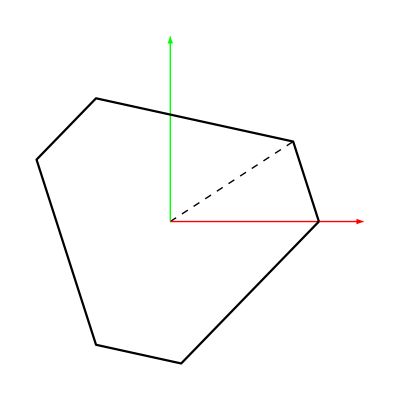

```mathematica
Show[Graphics[{Dashed, Line[{{0,0}, (b/.datap)[[2]][[1;;2]]}]}], Graphics[{Green, Arrow[{{0,0},{0,1.3}}]}],Graphics[{Red, Arrow[{{0,0},{1.3,0}}]}], ListLinePlot[Join[(b/.datap), {(b/.datap)[[1]]}][[;;, 1;;2]], PlotStyle->Black], AspectRatio->1, ImageResolution->600]
```

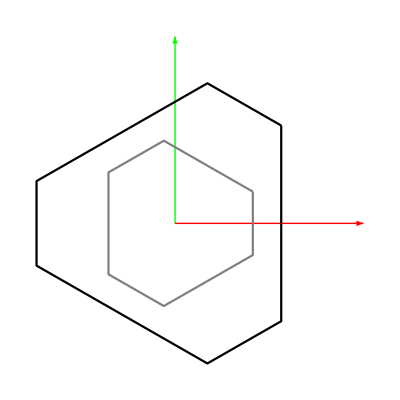

```mathematica
(*Assuming that the center of the global axis is in the center of the bottom plate and hence all the ground joints are denoted by bi and the top plate edges by ai*)
(*Locations of all the known ground joints*)
b1 = {rb, 0, 0};
b2 = rotZ[2*γb].b1;
b3 = rotZ[2π/3].b1;
b4 = rotZ[2π/3].b2;
b5 = rotZ[4π/3].b1;
b6 = rotZ[4π/3].b2;

tempb = Table[Symbol["b"<>ToString[i]],{i, 6}];

b = Table[rotZ[(2π/3-2*γb)/2].tempb[[i]],{i, Length[tempb]}];

al1 = {rt, 0, 0};
al2 = rotZ[2*γt].al1;
al3 = rotZ[2π/3].al1;
al4 = rotZ[2π/3].al2;
al5 = rotZ[4π/3].al1;
al6 = rotZ[4π/3].al2;
tempal = Table[Symbol["al"<>ToString[i]],{i, 6}];
al = Table[rotZ[(2π/3-2γt)/2].tempal[[i]],{i, Length[tempal]}];
Show[Graphics[{Green, Arrow[{{0,0},{0,1.3}}]}],Graphics[{Red, Arrow[{{0,0},{1.3,0}}]}], ListLinePlot[Join[(b/.datap), {(b/.datap)[[1]]}][[;;, 1;;2]], PlotStyle->Black],ListLinePlot[Join[(al/.datap), {(al/.datap)[[1]]}][[;;, 1;;2]],PlotStyle->Gray], AspectRatio->1, ImageResolution->600]
```

```mathematica
b/.datap
```

{{0.732576,0.680685,0},{0.223203,0.974772,0},{-0.955779,0.294087,0},{-0.955779,-0.294087,0},{0.223203,-0.974772,0},{0.732576,-0.680685,0}}

```mathematica
cords = {"x", "y", "z"};
```

```mathematica
acords = Table[Table[Symbol["a"<>ToString[j]<>cords[[i]]],{i, 3}],{j, 6}]
```

{{a1x,a1y,a1z},{a2x,a2y,a2z},{a3x,a3y,a3z},{a4x,a4y,a4z},{a5x,a5y,a5z},{a6x,a6y,a6z}}

```mathematica
Inner[Rule, Flatten[acords], Flatten[b/.datap], List]
```

{a1x→0.732576,a1y→0.680685,a1z→0,a2x→0.223203,a2y→0.974772,a2z→0,a3x→-0.955779,a3y→0.294087,a3z→0,a4x→-0.955779,a4y→-0.294087,a4z→0,a5x→0.223203,a5y→-0.974772,a5z→0,a6x→0.732576,a6y→-0.680685,a6z→0}

## Inverse Kinematics:

```mathematica
(*Assuming that the center of the global axis is in the center of the bottom plate and hence all the ground joints are denoted by bi and the top plate edges by ai*)
l= Table[Symbol["l"<>ToString[i]],{i, 6}];
(*a = Table[Symbol["a"<>ToString[i]],{i, 6}];*)
ϕ = Table[Symbol["ϕ"<>ToString[i]],{i,6}];
ψ = Table[Symbol["ψ"<>ToString[i]],{i,6}];
```

```mathematica
(*Considering ϕi, ψi and li's as the configuration space q*)
(*Rotation matrix of any leg li*)
Rl = Table[rotY[ϕ[[i]]].rotX[ψ[[i]]],{i, 6}];
(*Angular velocity Jacobian of each leg*)
Jωl = Table[SkewMat2vec[Simplify[T[Rl[[i]]].D[Rl[[i]],{Join[ϕ,ψ, l]}]]],{i, 6}];
(*a in global frame via b*)
a  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, l[[i]]},{i, 6}];
```

```mathematica
(*The mid point of the top platform will be*)
ptp = Total[a]/6;
```

```mathematica
(*(*Now consider the three points a1, a5, a6 so that the local orientation of the top platform is along the global frame*)
a65 = Simplify[((a[[6]]-a[[5]])/Sqrt[((b[[6]]-b[[5]]).(b[[6]]-b[[5]]))/.rb->rt/.γb->γt])];
a15 = Simplify[((a[[1]]-a[[5]])/Sqrt[((b[[1]]-b[[5]]).(b[[1]]-b[[5]]))/.rb->rt/.γb->γt])];
(*a12 and a13 are unit vectors, but the cross need not be a unit vector and hence the Rotation matrix columns need to be re-normalised*)
(*We need to find the magnitude of the second and the third axes*)*)
```

```mathematica
(*Now consider the three points a1, a5, a6 so that the local orientation of the top platform is along the global frame*)
a56 = Simplify[((a[[5]]-a[[6]])/Sqrt[((b[[5]]-b[[6]]).(b[[5]]-b[[6]]))/.rb->rt/.γb->γt])];
a16 = Simplify[((a[[1]]-a[[6]])/Sqrt[((b[[1]]-b[[6]]).(b[[1]]-b[[6]]))/.rb->rt/.γb->γt])];
```

```mathematica
(*sinangle = Simplify[(Cross[(b[[6]]-b[[5]])/Sqrt[(b[[6]]-b[[5]]).(b[[6]]-b[[5]])], (b[[1]]-b[[5]])/Sqrt[(b[[1]]-b[[5]]).(b[[1]]-b[[5]])]]/.rb->rt/.γb->γt)[[3]]];
zaxis = Simplify[Cross[a65, a15]/sinangle];
Rtp = {a65,  Cross[zaxis, a65], zaxis};*)
```

```mathematica
sinangle = Simplify[(Cross[(b[[1]]-b[[6]])/Sqrt[(b[[1]]-b[[6]]).(b[[1]]-b[[6]])], (b[[5]]-b[[6]])/Sqrt[(b[[5]]-b[[6]]).(b[[5]]-b[[6]])]]/.rb->rt/.γb->γt)[[3]]];
zaxis = Simplify[Cross[a16, a56]/sinangle];
Rtp = { Cross[a16, zaxis],a16, zaxis};
```

```mathematica
(*Now that we have obtained the rotation matrix, we can find the angular velocity Jacobian of the top plate*)
Jωt = SkewMat2vec[T[Rtp].D[Rtp,{Join[ϕ, ψ, l]}]];
```

```mathematica
(*CoM of the two parts of the prismatic joints*)
pa  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, l[[i]]-la/2},{i, 6}];
pb  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, lb/2},{i, 6}];
(*First case where ϕi, ψi and li's are given. Contains all the Jacobians*)
Jpai = D[pa, {Join[ϕ, ψ, l]}];
Jpbi = D[pb, {Join[ϕ, ψ, l]}];
Jtp = D[ptp,  {Join[ϕ, ψ, l]}];
```

```mathematica
(*To generate the test data for this system*)
tpdat = {c1->0, c2->0, c3->0, x->0, y->0, z->1.1};
```

```mathematica
qrule =Flatten[Table[{ϕ[[i]]-> ϕ[[i]][t], ψ[[i]]->ψ[[i]][t], l[[i]]->l[[i]][t]},{i, 6}]];
q = Join[ϕ, ψ, l]/.qrule;
```

```mathematica
Amat = vec2SkewMat[{c1, c2, c3}];
Rdat = Simplify[Inverse[(IdentityMatrix[3]-Amat)].(IdentityMatrix[3]+Amat)];
Simplify[Rdat.T[Rdat]]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
Rtps = Rtp/.qrule/.datap/.leglparam/.legmparam/.tpmparam/.tpdat;
aldat = al/.datap;
ag =Simplify[Table[{x, y, z}+Rdat.aldat[[i]],{i, 6}]]/.tpdat;
bdat = b/.datap;
```

```mathematica
(*Formulating the constraint equations*)
```

```mathematica
η1 = Join[Simplify[Expand[Table[(a[[i]]-a[[i+1]]).(a[[i]]-a[[i+1]])-(al[[i]]-al[[i+1]]).(al[[i]]-al[[i+1]]),{i, 5}]]], {Simplify[Expand[(a[[6]]-a[[1]]).(a[[6]]-a[[1]])-(al[[6]]-al[[1]]).(al[[6]]-al[[1]])]], Simplify[Expand[(a[[1]]-a[[3]]).(a[[1]]-a[[3]])-(al[[3]]-al[[1]]).(al[[3]]-al[[1]])]], Simplify[Expand[(a[[1]]-a[[4]]).(a[[1]]-a[[4]])-(al[[1]]-al[[4]]).(al[[1]]-al[[4]])]], Simplify[Expand[(a[[1]]-a[[5]]).(a[[1]]-a[[5]])-(al[[1]]-al[[5]]).(al[[1]]-al[[5]])]], Expand[(a[[1]]-a[[3]]).Cross[a[[1]]-a[[2]], a[[1]]-a[[4]]]], Expand[(a[[1]]-a[[4]]).Cross[a[[1]]-a[[3]], a[[1]]-a[[5]]]], Expand[(a[[1]]-a[[5]]).Cross[a[[1]]-a[[4]], a[[1]]-a[[6]]]]}];
```

```mathematica
ηconfig = η1/.datap/.leglparam/.legmparam/.tpmparam/.qrule;
```

```mathematica
(*Therefore the sample solution satisfies the constraint equations*)
```

```mathematica
(*ηconfig/.datap/.leglparam/.legmparam/.tpmparam/.sampledat/.qrule*)
```

```mathematica
p = Table[Symbol["p"<>ToString[i]],{i,6}]; (*p is tan ϕ/2*)
s = Table[Symbol["s"<>ToString[i]],{i,6}]; (*s is tan ψ/2*)
```

```mathematica
htanrule = Flatten[Table[{Cos[ϕ[[i]][t]]->(1-p[[i]]^2)/(1+p[[i]]^2),Sin[ϕ[[i]][t]]->(2*p[[i]])/(1+p[[i]]^2), Cos[ψ[[i]][t]]->(1-s[[i]]^2)/(1+s[[i]]^2),Sin[ψ[[i]][t]]->(2*s[[i]])/(1+s[[i]]^2) },{i,6}]];
```

```mathematica
(*iksolver module*)
```

```mathematica
als = {{al1x, al1y, 0}, {al2x, al2y, 0}, {al3x, al3y, 0}, {al4x, al4y, 0}, {al5x, al5y, 0}, {al6x, al6y, 0}};
bs = {{b1x, b1y, 0}, {b2x, b2y, 0}, {b3x, b3y, 0}, {b4x, b4y, 0}, {b5x, b5y, 0}, {b6x, b6y, 0}};
```

```mathematica
alsrules = Inner[Rule, Flatten[als[[;;, 1;;2]]], Flatten[al[[;;, 1;;2]]], List];
bsrules = Inner[Rule, Flatten[bs[[;;, 1;;2]]], Flatten[b[[;;, 1;;2]]], List];
```

```mathematica
atps = Table[pc+Rtp2.als[[i]],{i,6}];
ajs = Table[bs[[i]]+Rl[[i]].{0,0,l[[i]]},{i, 6}];
```

```mathematica
Arp = vec2SkewMat[{c1, c2, c3}];
Rtp2 = Simplify[Inverse[(IdentityMatrix[3]-Arp)].(IdentityMatrix[3]+Arp)];
pc = {x, y, z};
aj  = Table[b[[i]]+Rl[[i]].{0,0, l[[i]]},{i, Length[b]}];
atp = Table[pc+Rtp2.al[[i]],{i, Length[al]}];
```

```mathematica
(*Formulating constraints in the extended configuration space*)
```

```mathematica
ηext = Flatten[(aj-atp)]/.datap/.leglparam;
```

```mathematica
SetSystemOptions["SimplificationOptions"->"AutosimplifyTrigs"->False];
```

```mathematica
qx = {x, y, z, c1, c2, c3};
```

```mathematica
samplex = Inner[Rule, qx, {0,0,0.75,0,0,0}, List];
```

```mathematica
li2 = Table[(atp-bs)[[i]].(atp-bs)[[i]],{i, 6}];
li = Sqrt[Together[li2]];
lirule = Inner[Rule, l, li,List];
```

```mathematica
lval = Inner[Rule, l, Simplify[li/.alsrules/.bsrules/.datap], List];
clval = Compile[{{x, _Complex},{y, _Complex},{z, _Complex},{c1, _Complex},{c2, _Complex},{c3, _Complex}}, Evaluate[l/.lval]];
```

```mathematica
sinψ = Together[Table[Simplify[(atp[[i]][[2]]-Expand[aj[[i]][[2]]][[;;-2]])/(-l[[i]])], {i, 6}]];
cos2ψ = Table[((atp[[i]][[1]]-Expand[aj[[i]][[1]]][[;;-2]])/l[[i]])^2+(atp[[i]][[3]]/l[[i]])^2,{i, 6}];
cosψ = Sqrt[Together[cos2ψ]];
sinψrule = Inner[Rule, Table[Sin[ψ[[i]]],{i, 6}], sinψ, List];
cosψrule = Inner[Rule, Table[Cos[ψ[[i]]],{i, 6}], cosψ, List];
```

```mathematica
ψval = Inner[Rule, ψ, Simplify[Table[ArcTan[cosψ[[i]], sinψ[[i]]],{i, 6}]/.alsrules/.bsrules/.datap], List];
```

```mathematica
cψval = Compile[{{x, _Complex},{y, _Complex},{z, _Complex},{c1, _Complex},{c2, _Complex},{c3, _Complex},{l1, _Complex},{l2, _Complex},{l3, _Complex},{l4, _Complex},{l5, _Complex},{l6, _Complex}}, Evaluate[ψ/.ψval]];
```

```mathematica
sinϕ = Together[Table[(atp[[i]][[1]]-Expand[aj[[i]][[1]]][[;;-2]])/(li[[i]]*Cos[ψ[[i]]]),{i, 6}]];
cosϕ = Table[(atp[[i]][[3]])/(li[[i]]*Cos[ψ[[i]]]),{i, 6}];
```

```mathematica
sinϕrule = Inner[Rule, Table[Sin[ϕ[[i]]],{i, 6}], sinϕ, List];
cosϕrule = Inner[Rule, Table[Cos[ϕ[[i]]],{i, 6}], cosϕ, List];
```

```mathematica
ϕval = Inner[Rule, ϕ, Simplify[Table[ArcTan[cosϕ[[i]], sinϕ[[i]]],{i, 6}]/.alsrules/.bsrules/.datap], List];
```

```mathematica
cϕval = Compile[{{x, _Complex},{y, _Complex},{z, _Complex},{c1, _Complex},{c2, _Complex},{c3, _Complex},{ψ1, _Complex},{ψ2, _Complex},{ψ3, _Complex},{ψ4, _Complex},{ψ5, _Complex},{ψ6, _Complex}}, Evaluate[ϕ/.ϕval]];
```

```mathematica
iksolC[x_] := Module[{lvals, ψvals, ϕvals, xrule, lrule, ψrule},
xrule = Inner[Rule, qx, x, List];
lvals = l/.lval/.xrule;
lrule = Inner[Rule, l, lvals, List];
ψvals = ψ/.ψval/.Join[xrule, lrule];
ψrule = Inner[Rule, ψ, ψvals, List];
ϕvals = ϕ/.ϕval/.Join[xrule,ψrule];
Return[Join[ϕvals, ψvals, lvals]]
]
```

```mathematica
(*verifying roots taken from Anirbans codes*)
```

```mathematica
roots = ({{x->0.21833808165665786, y->-0.7906213868033382, z->0.7240859710802774, c1->-0.7154994439464201, c2->-0.6452575011458942, c3->0}, {x->0.20000000000000112, y->0, z->1.2799999999999998, c1->0.19999999999999996, c2->0, c3->0}, {x->-0.5136951579345258, y->-0.5199956193725788, z->-0.7987229831575837, c1->-0.3337590445754842, c2->-0.9516994614991616, c3->0}, {x->0.5244336967602403, y->0.26850949397918333, z->1.0307988965821262, c1->0.6037494337274671, c2->-0.18856114122522924, c3->0}, {x->0.20000000000000112, y->0, z->-1.2799999999999998, c1->-0.19999999999999996, c2->0, c3->0}, {x->-0.5136951579345258, y->-0.5199956193725788, z->0.7987229831575837, c1->0.3337590445754842, c2->0.9516994614991616, c3->0}, {x->0.21833808165665786, y->-0.7906213868033382, z->-0.7240859710802774, c1->0.7154994439464201, c2->0.6452575011458942, c3->0}, {x->0.5244336967602403, y->0.26850949397918333, z->-1.0307988965821262, c1->-0.6037494337274671, c2->0.18856114122522924, c3->0}});
```

```mathematica
rootsC = ({{x->1.8700438348728161, y->-0.5235870043873335, z->0.-0.926898973258719 ⅈ, c1->0.-0.10569096861540776 ⅈ, c2->0.+0.7154784037290103 ⅈ, c3->0}, {x->1.8700438348728161, y->-0.5235870043873335, z->0.+0.926898973258719 ⅈ, c1->0.+0.10569096861540776 ⅈ, c2->0.-0.7154784037290103 ⅈ, c3->0}, {x->-1.0720337007448544, y->1.6971275035884408, z->0.-0.9685245785328371 ⅈ, c1->0.-0.6638886705593215 ⅈ, c2->0.-0.3422565386596551 ⅈ, c3->0}, {x->-1.0720337007448544, y->1.6971275035884408, z->0.+0.9685245785328371 ⅈ, c1->0.+0.6638886705593215 ⅈ, c2->0.+0.3422565386596551 ⅈ, c3->0}, {x->0.21833808165665786, y->-0.7906213868033382, z->0.7240859710802774, c1->-0.7154994439464201, c2->-0.6452575011458942, c3->0}, {x->0.20000000000000112, y->0, z->1.2799999999999998, c1->0.19999999999999996, c2->0, c3->0}, {x->-0.5136951579345258, y->-0.5199956193725788, z->-0.7987229831575837, c1->-0.3337590445754842, c2->-0.9516994614991616, c3->0}, {x->0.5244336967602403, y->0.26850949397918333, z->1.0307988965821262, c1->0.6037494337274671, c2->-0.18856114122522924, c3->0}, {x->-0.7337396637589878, y->-2.1544767236034987, z->0.-1.3894731322781502 ⅈ, c1->0.+0.6338547336758182 ⅈ, c2->0.-0.42758251604766423 ⅈ, c3->0}, {x->-0.7337396637589878, y->-2.1544767236034987, z->0.+1.3894731322781502 ⅈ, c1->0.-0.6338547336758182 ⅈ, c2->0.+0.42758251604766423 ⅈ, c3->0}, {x->0.20000000000000112, y->0, z->-1.2799999999999998, c1->-0.19999999999999996, c2->0, c3->0}, {x->-0.5136951579345258, y->-0.5199956193725788, z->0.7987229831575837, c1->0.3337590445754842, c2->0.9516994614991616, c3->0}, {x->0.21833808165665786, y->-0.7906213868033382, z->-0.7240859710802774, c1->0.7154994439464201, c2->0.6452575011458942, c3->0}, {x->0.5244336967602403, y->0.26850949397918333, z->-1.0307988965821262, c1->-0.6037494337274671, c2->0.18856114122522924, c3->0}});
```

```mathematica
ikroots = Table[Inner[Rule, Join[ϕ, ψ, l], iksolC[qx/.roots[[i]]], List], {i, Length[roots]}];
```

```mathematica
iksolC[x_] := Module[{lval, ψval, ϕval},
lval = clval@@x;
ψval = cψval@@Join[x, lval];
ϕval = cϕval@@Join[x,ψval];
Return[Join[ϕval, ψval, lval]]
]
```

```mathematica
xbrule = Table[{Symbol["xb"<>ToString[i]], Symbol["yb"<>ToString[i]], Symbol["zb"<>ToString[i]]},{i, 1, 6}];
xtrule = Table[{Symbol["xt"<>ToString[i]], Symbol["yt"<>ToString[i]], Symbol["zt"<>ToString[i]]},{i, 1, 6}];
```

```mathematica
top = Table[Inner[Rule, xtrule[[i]], (a/.datap/.ikroots[[1]])[[i]], List],{i, 1, 6}]
```

{{xt1→0.628916,yt1→-0.430149,zt1→0.91962},{xt2→0.449784,yt2→-0.557918,zt2→0.245515},{xt3→0.127107,yt3→-0.844307,zt3→0.153522},{xt4→-0.212447,yt4→-1.17689,zt4→0.679753},{xt5→-0.101009,yt5→-1.09741,zt5→1.09912},{xt6→0.417678,yt6→-0.637052,zt6→1.24699}}

```mathematica
base = Table[Inner[Rule, xbrule[[i]], (b/.datap/.ikroots[[1]])[[i]], List],{i, 1, 6}]
```

{{xb1→0.732576,yb1→0.680685,zb1→0},{xb2→0.223203,yb2→0.974772,zb2→0},{xb3→-0.955779,yb3→0.294087,zb3→0},{xb4→-0.955779,yb4→-0.294087,zb4→0},{xb5→0.223203,yb5→-0.974772,zb5→0},{xb6→0.732576,yb6→-0.680685,zb6→0}}

```mathematica
roots[[1]]
```

{x→0.218338,y→-0.790621,z→0.724086,c1→-0.715499,c2→-0.645258,c3→0}

```mathematica
Rationalize[base, 0.01]
```

{{xb1→8/11,yb1→11/16,zb1→0},{xb2→2/9,yb2→28/29,zb2→0},{xb3→-19/20,yb3→2/7,zb3→0},{xb4→-19/20,yb4→-2/7,zb4→0},{xb5→2/9,yb5→-29/30,zb5→0},{xb6→8/11,yb6→-13/19,zb6→0}}

```mathematica
Max[Table[ηconfig/.qrule/.datap/.leglparam/.legmparam/.tpmparam/.ikroots[[i]], {i, Length[ikroots]}]];
```

```mathematica
roots//Dimensions
```

{8,6}

```mathematica
(*All the roots satisfy our constraint equation*)
```

```mathematica
(*{x->x[t], y->y[t], z->z[t], c1->c1[t], c2->c2[t], c3->c3[t]}*)
```

## Plotting the SRSPM:

```mathematica
qrule = Inner[Rule, q, Join[ϕ, ψ, l], List];
qvar = q/.qrule;
```

```mathematica
qfull = Join[qx, qvar];
```

```mathematica
(*Plotting SRSPM from discretisation starting position*)
```

```mathematica
plotsrspm[qvals_]:=Module[{base, top, llinks, jointsbase, jointstop,jlist,bval,aval, direction, tempvec,lbinks,lainks, axis},
(*Base and top plate*)
bval = N[b/.datap];
aval = N[a/.datap/.leglparam];
tempvec  = Table[(aval[[i]]-bval[[i]])/.qvals,{i, 6}];
direction = Table[(tempvec[[i]])/Norm[tempvec[[i]]],{i, 6}];

base = Graphics3D[{Gray,Opacity[0.3],Polygon[bval]},SphericalRegion->True, Boxed->False, PlotRange->{{-1.6, 1.6}, {-1.6, 1.6}, {-1.6, 1.6}}];
top = Graphics3D[{Gray,Opacity[0.8], Polygon[Chop[aval/.qvals]]},Boxed->False];
(*Links*)
lbinks = Table[Graphics3D[{Purple,Opacity[0.3],Cylinder[{bval[[i]],bval[[i]]+direction[[i]]*lb/.leglparam}, 0.05]}],{i, Length[bval]}];
(*lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, bval[[i]]/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];*)
lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, aval[[i]]-direction[[i]]*la/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];
(*Joints*)
jointsbase = Table[Graphics3D[Sphere[bval[[i]]/.qvals, 0.06]],{i, Length[bval]}];
jointstop = Table[Graphics3D[Sphere[aval[[i]]/.qvals, 0.06]],{i, Length[bval]}];(*Plotting the axis on the manipulator*)
axis = Show[Graphics3D[{Red,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{1,0,0}},0.02]]}], Graphics3D[{Green,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,1,0}},0.02]]}], 
Graphics3D[{Blue,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,0,1}},0.02]]}]
];
(*Plotting the configuration*);
Show[base, top, jointstop, jointsbase, lainks, lbinks, axis]
]
```

```mathematica
(*Plotting the constraints*)
```

```mathematica
plotconstraints[qvals_]:=Module[{base, top, llinks, jointsbase, jointstop,jlist,bval,aval, direction, tempvec,lbinks,lainks, axis, constraints, oval, pts},
oval=5;
(*Base and top plate*)
bval = N[b/.datap];
aval = N[a/.datap/.leglparam];
tempvec  = Table[(aval[[i]]-bval[[i]])/.qvals,{i, 6}];
direction = Table[(tempvec[[i]])/Norm[tempvec[[i]]],{i, 6}];

base = Graphics3D[{Gray,Opacity[0.3],Polygon[bval]},SphericalRegion->True, Boxed->False, PlotRange->{{-1.6, 1.6}, {-1.6, 1.6}, {-1.6, 1.6}}];
top = Graphics3D[{Gray,Opacity[0.8], Polygon[Chop[aval/.qvals]]},Boxed->False];
(*Links*)
lbinks = Table[Graphics3D[{Purple,Opacity[0.3/oval],Cylinder[{bval[[i]],bval[[i]]+direction[[i]]*lb/.leglparam}, 0.05]}],{i, 2,6}];
(*lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, bval[[i]]/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];*)
lainks = Table[Graphics3D[{LightOrange,Opacity[0.85/oval],Cylinder[{aval[[i]]/.qvals, aval[[i]]-direction[[i]]*la/.leglparam/.qvals}, 0.03]}],{i, 2,6}];
(*Joints*)
jointsbase = Table[Graphics3D[{Opacity[1/oval],Sphere[bval[[i]]/.qvals, 0.06]}],{i, Length[bval]}];
jointstop = Table[Graphics3D[{Opacity[1/oval],Sphere[aval[[i]]/.qvals, 0.06]}],{i, Length[bval]}];(*Plotting the axis on the manipulator*)
axis = Show[Graphics3D[{Red, Opacity[0.5/oval],Arrowheads[0.04],Arrow[Tube[{{0,0,0},{1,0,0}},0.02]]}], Graphics3D[{Green, Opacity[0.5/oval],Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,1,0}},0.02]]}], 
Graphics3D[{Blue, Opacity[0.5/oval],Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,0,1}},0.02]]}]
];
(*Plotting constraints*)
constraints = Show[Graphics3D[{Gray,Arrowheads[0.04],Arrow[Tube[{{0,0,0},bval[[1]]},0.025]]}], Graphics3D[{Purple,Arrowheads[0.045],Arrow[Tube[{bval[[1]], (aval/.qvals)[[1]]},0.025]]}], Graphics3D[{Black,Arrowheads[0.045],Arrow[Tube[{(aval/.qvals)[[1]], {x,y,z}/.qvals},0.025]]}], Graphics3D[{Brown,Arrowheads[0.045],Arrow[Tube[{{0,0,0}, {x,y,z}/.qvals},0.025]]}]];
(*Mid points*)
pts = Show[Graphics3D[{Red, Opacity[0.5],Sphere[{0,0,0}, 0.06]}], Graphics3D[{Red, Opacity[0.5],Sphere[Mean[aval/.qvals], 0.06]}]];
(*Plotting the configuration*);
Show[base, top, jointstop, jointsbase, lainks, lbinks, axis, constraints, pts]
]
```

```mathematica
pt = {0.2,0.2,1.1,0.1,0,0}
cpose = Inner[Rule, qfull,  Join[pt, iksolC[pt]], List];
plotconstraints[Chop[cpose]]
```

{0.2,0.2,1.1,0.1,0,0}

-Graphics3D-

```mathematica
index = 2;
initpose = Join[qx/.roots[[index]], iksolC[qx/.roots[[index]]]];
plotsrspm[Chop[Inner[Rule, qfull, initpose, List]]]
```

-Graphics3D-

```mathematica
(*To plot only the top platform*)
```

```mathematica
(*plotsrspm[qvals_]:=Module[{base, top, llinks, jointsbase, jointstop,jlist,bval,aval, direction, tempvec,lbinks,lainks, axis},
(*Base and top plate*)
bval = N[b/.datap];
aval = N[a/.datap/.leglparam];
tempvec  = Table[(aval[[i]]-bval[[i]])/.qvals,{i, 6}];
direction = Table[(tempvec[[i]])/Norm[tempvec[[i]]],{i, 6}];

base = Graphics3D[{Gray,Opacity[0.8],Polygon[bval]},SphericalRegion->True, Boxed->False, PlotRange->{{-1.6, 1.6}, {-1.6, 1.6}, {-1.6, 1.6}}];
top = Graphics3D[{Gray,Opacity[0.8], Polygon[Chop[aval/.qvals]]},Boxed->False];
(*Links*)
lbinks = Table[Graphics3D[{Purple,Opacity[0.3],Cylinder[{bval[[i]],bval[[i]]+direction[[i]]*lb/.leglparam}, 0.05]}],{i, Length[bval]}];
(*lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, bval[[i]]/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];*)
lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, aval[[i]]-direction[[i]]*la/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];
(*Joints*)
jointsbase = Table[Graphics3D[Sphere[bval[[i]]/.qvals, 0.06]],{i, Length[bval]}];
jointstop = Table[Graphics3D[Sphere[aval[[i]]/.qvals, 0.06]],{i, Length[bval]}];(*Plotting the axis on the manipulator*)
axis = Show[Graphics3D[{Red,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{1,0,0}},0.02]]}], Graphics3D[{Green,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,1,0}},0.02]]}], 
Graphics3D[{Blue,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,0,1}},0.02]]}]
];
(*Plotting the configuration*);
Show[base, axis]
]*)
```

```mathematica
(*Select a circle, do the IK and get the values and fit a function to those leg values. Now track these functions with other initial conditions*)
```

## Newton-Raphson method for root tracking

```mathematica
scale = 0.2;
parampath = {scale*Cos[α], scale*Sin[α], 1.28, scale*1, scale*0,scale*0};
```

```mathematica
pathpts = Table[parampath/.α->ii, {ii, 0, 2π, 2π/50}];
```

```mathematica
iksolC[pathpts[[1]]][[-6;;]]
```

{1.44582+0. ⅈ,1.56868+0. ⅈ,1.57865+0. ⅈ,1.33939+0. ⅈ,1.15248+0. ⅈ,1.28688+0. ⅈ}

```mathematica
Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[pathpts[[u]], iksolC[pathpts[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[pathpts[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[pathpts], 1}]
```

```mathematica
(*Selected pose for plotting*)
```

```mathematica
(*plotsrspm[Inner[Rule, qfull, Join[pathpts[[43]], iksol[pathpts[[43]]]], List]]*)
```

### Real roots:

```mathematica
(*get all the leg array for the circular motion*)
```

```mathematica
(*legvals = Table[Join[{i-1}, {iksol[pathpts[[i]]][[-6;;]]}], {i, Length[pathpts]}];*)
legvals = Table[iksolC[pathpts[[i]]][[-6;;]], {i, Length[pathpts]}];
```

```mathematica
(*legfunc = Interpolation[legvals]*)
```

```mathematica
(*Now root tracking all the 8 solutions with this leg interpolation for the 50 points*)
```

```mathematica
(*Newton-Raphson method*)
```

```mathematica
Inner[List, q/.qrule, Table[_Complex, {i, Length[q]}], List]
```

{{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}

```mathematica
cηconfig =  Compile[{{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[ηconfig/.qrule], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
Jηconfig = D[ηconfig/.qrule,{ q[[;;-7]]/.qrule}];
```

```mathematica
cJηconfig =  Compile[{{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[Jηconfig], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
NRTracking[thetai_, phii_, eta_, Jeta_] :=  Module[{nvec, Jmat, δphi, loopcounter, tempphi},
(*Takes in eta and Jeta as compiled functions*)
nvec = eta@@Join[phii, thetai];
loopcounter=0;
tempphi = phii;
While[Norm[nvec]≥ 10^-10,
If[loopcounter≥ 100, Break];
loopcounter++;
Jmat =  Jeta@@Join[tempphi, thetai];
δphi=LinearSolve[Jmat,nvec];
tempphi =tempphi-δphi;
nvec = eta@@Join[tempphi, thetai];
];
Return[tempphi];
]
```

```mathematica
testconfig = initpose[[7;;-7]];
```

```mathematica
tic[]
tempϕ = testconfig;
ϕlist = {tempϕ};
For[i=2,i≤Length[legvals], i++, 
tempϕ = NRTracking[legvals[[i]], tempϕ, cηconfig, cJηconfig];
AppendTo[ϕlist, tempϕ];
]
toc[]
```

Actual time consumed: 0.070998 seconds.

CPU time consumed: 0.054118 seconds.

```mathematica
(*Tracking using the extended configuration space*)
```

```mathematica
Inner[List, Join[qx, q/.qrule], Table[_Complex, {i, Length[Join[qx, q]]}], List]
```

{{x,_Complex},{y,_Complex},{z,_Complex},{c1,_Complex},{c2,_Complex},{c3,_Complex},{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}

```mathematica
cηext =  Compile[{{x,_Complex},{y,_Complex},{z,_Complex},{c1,_Complex},{c2,_Complex},{c3,_Complex},{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[ηext], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
Jηext = D[ηext,{ Join[qx, q[[;;-7]]/.qrule]}];
```

```mathematica
cJηext =  Compile[{{x,_Complex},{y,_Complex},{z,_Complex},{c1,_Complex},{c2,_Complex},{c3,_Complex},{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[Jηext], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
testext = initpose[[;;-7]];
tic[]
tempϕ = testext;
ϕlist = {tempϕ};
For[i=2,i≤Length[legvals], i++, 
tempϕ = NRTracking[legvals[[i]], tempϕ, cηext, cJηext];
AppendTo[ϕlist, tempϕ];
]
toc[]
```

Actual time consumed: 0.03813 seconds.

CPU time consumed: 0.032777 seconds.

```mathematica
xlist = ϕlist[[;;, ;;3]];
```

```mathematica
xlist[[1]]
```

{0.2,0,1.28}

```mathematica
Graphics3D[Sphere[{Chop[xlist[[1;;]]]}, 0.01]]
```

-Graphics3D-

```mathematica
initposes = Table[Join[qx/.roots[[i]], iksolC[qx/.roots[[i]]]], {i, Length[roots]}];
```

```mathematica
testext = initposes[[2]][[;;-7]];
tic[]
tempϕ = testext;
ϕlist = {tempϕ};
For[i=2,i≤Length[legvals], i++, 
tempϕ = NRTracking[legvals[[i]], tempϕ, cηext, cJηext];
AppendTo[ϕlist, tempϕ];
]
toc[]
```

Actual time consumed: 0.03426 seconds.

CPU time consumed: 0.034065 seconds.

```mathematica
xlist = ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksolC[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[pathpts], 1}]
```

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

```mathematica
(*Tracking all the sets of roots together*)
```

```mathematica
testext = initposes[[;;, ;;-7]];
tic[]
tempϕ = testext;
ϕlist = {tempϕ};
For[i=2,i≤Length[legvals], i++, 
tempϕ = Table[NRTracking[legvals[[i]], tempϕ[[j]], cηext, cJηext],{j, Length[tempϕ]}];
AppendTo[ϕlist, tempϕ];
]
toc[]
```

Actual time consumed: 0.26147 seconds.

CPU time consumed: 0.261515 seconds.

```mathematica
tempU = 51;
Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[tempU]], iksolC[xlist[[tempU]]]], List]],ViewAngle->Automatic,ViewCenter->{0.5,0.5,0.5},ViewMatrix->Automatic,ViewPoint->{-1.436630585725502,-2.436545269611847,1.857239809311155},ViewProjection->Automatic,ViewRange->All,ViewVector->Automatic,ViewVertical->{-0.029245185453707287,-0.04235819972678877,0.9986743723775453}]
```

-Graphics3D-

### Complex roots:

```mathematica
scale = 0.2;
(*parampath = {scale*Cos[α], scale*Sin[α], 1.28, scale*1, scale*0,scale*0};*)
parampath={scale*Cos[α],scale*Sin[α],1.28,scale*Cos[α],scale*Sin[α],scale*Sin[2*α]};
```

```mathematica
pathpts = Table[parampath/.α->ii, {ii, 0, 2π, 2π/50}];
```

```mathematica
Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[pathpts[[u]], iksolC[pathpts[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[pathpts[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[pathpts], 1}]
```

```mathematica
legvals = Table[iksolC[pathpts[[i]]][[-6;;]], {i, Length[pathpts]}];
```

```mathematica
(* Now tracking the other roots *)
```

```mathematica
posesC = Table[Join[qx/.rootsC[[i]], iksolC[qx/.rootsC[[i]]]], {i, Length[rootsC]}];
```

```mathematica
posesC[[1]][[;;-7]]//CForm;
```

```mathematica
(*LinearSolve overflow occured in computation because of the usage of Max and abs instead of norm in NRTracker*)
```

```mathematica
posesC//Dimensions
```

{14,24}

```mathematica
iter = 18;
testext = posesC[[1]][[;;-7]];
tic[]
tempϕ = testext;
ϕlist = {tempϕ};
For[i=2,i≤iter, i++, 
tempϕ = NRTracking[legvals[[i]], tempϕ,cηext,cJηext];
AppendTo[ϕlist, tempϕ];
]
toc[]
```

Actual time consumed: 0.008869 seconds.

CPU time consumed: 0.008875 seconds.

```mathematica
(*Bringing in the singluarity manifold*)
```

```mathematica
g11 = ToExpression[Import["srspm_pos_eq1.txt"]]
```

0.00218325+0.00530428 x-0.0120075 x^2-0.00132539 y-0.0292269 x y-0.0124698 y^2-0.0375001 z+0.073172 x z+0.0108431 x^2 z+0.0412325 y z+0.0468517 x y z+0.0497715 y^2 z+0.0285304 z^2-0.10733 x z^2-0.217641 y z^2+0.205157 z^3

```mathematica
lim=4;
cp=ContourPlot3D[g11==0,{x,-lim,lim},{y,-lim,lim},{z,-lim,lim},ContourStyle->Green,PlotPoints->60];
```

```mathematica
(*xpose = {0,0,0.1,0.2,0,0};
Show[plotsrspm[Inner[Rule, qfull, Join[xpose, iksolC[xpose]], List]], cp]*)
```

```mathematica
(*xpose = {0,0,0.1,0.2,0,0};
Show[plotsrspm[Inner[Rule, qfull, Join[xpose, iksolC[xpose]], List]], cp]*)
```

```mathematica
(*Now finding the roots that intersect*)
```

```mathematica
posesC//Chop//MatrixForm
```

(1.87004 | -0.523587 | 0.-0.926899 ⅈ | 0.-0.105691 ⅈ | 0.+0.715478 ⅈ | 0 | 1.5708+1.5263 ⅈ | 1.5708+0.691399 ⅈ | 1.5708-0.199792 ⅈ | 1.5708-0.523049 ⅈ | 1.5708+0.377184 ⅈ | 1.5708+1.39851 ⅈ | 0.58897 | 0.627358 | 0.384532 | 0.591043 | 0.152795 | -0.0749872 | 1.44582 | 1.56868 | 1.57865 | 1.33939 | 1.15248 | 1.28688
1.87004 | -0.523587 | 0.+0.926899 ⅈ | 0.+0.105691 ⅈ | 0.-0.715478 ⅈ | 0 | 1.5708-1.5263 ⅈ | 1.5708-0.691399 ⅈ | 1.5708+0.199792 ⅈ | 1.5708+0.523049 ⅈ | 1.5708-0.377184 ⅈ | 1.5708-1.39851 ⅈ | 0.58897 | 0.627358 | 0.384532 | 0.591043 | 0.152795 | -0.0749872 | 1.44582 | 1.56868 | 1.57865 | 1.33939 | 1.15248 | 1.28688
-1.07203 | 1.69713 | 0.-0.968525 ⅈ | 0.-0.663889 ⅈ | 0.-0.342257 ⅈ | 0 | -1.5708-0.79459 ⅈ | 3.14159-0.891289 ⅈ | -3.14159-0.461391 ⅈ | -3.14159-0.948897 ⅈ | -1.5708+1.03751 ⅈ | -1.5708+0.855051 ⅈ | -0.891722 | -1.5708+1.05398 ⅈ | -1.5708+1.23224 ⅈ | -1.5708+0.304463 ⅈ | -1.10481 | -1.13345 | 1.44582 | 1.56868 | 1.57865 | 1.33939 | 1.15248 | 1.28688
-1.07203 | 1.69713 | 0.+0.968525 ⅈ | 0.+0.663889 ⅈ | 0.+0.342257 ⅈ | 0 | -1.5708+0.79459 ⅈ | 0.+0.891289 ⅈ | 0.+0.461391 ⅈ | 0.+0.948897 ⅈ | -1.5708-1.03751 ⅈ | -1.5708-0.855051 ⅈ | -0.891722 | -1.5708+1.05398 ⅈ | -1.5708+1.23224 ⅈ | -1.5708+0.304463 ⅈ | -1.10481 | -1.13345 | 1.44582 | 1.56868 | 1.57865 | 1.33939 | 1.15248 | 1.28688
0.218338 | -0.790621 | 0.724086 | -0.715499 | -0.645258 | 0 | -0.112247 | 0.745313 | 1.42996 | 0.830045 | -0.28684 | -0.247355 | 0.876191 | 1.35618 | 0.805412 | 0.719639 | 0.106613 | -0.0339125 | 1.44582 | 1.56868 | 1.57865 | 1.33939 | 1.15248 | 1.28688
0.2 | 0 | 1.28 | 0.2 | 0 | 0 | 0.00305624 | -0.0668855 | 0.456963 | 0.546956 | -0.0946901 | 0.00349011 | 0.336276 | 0.286891 | -0.0210274 | 0.0247844 | -0.395383 | -0.379795 | 1.44582 | 1.56868 | 1.57865 | 1.33939 | 1.15248 | 1.28688
-0.513695 | -0.519996 | -0.798723 | -0.333759 | -0.951699 | 0 | -1.88547 | -2.65366 | 2.78228 | 2.89251 | -2.20522 | -1.74294 | 0.61606 | 0.697469 | 0.419763 | 0.5377 | 0.0705025 | -0.103948 | 1.44582 | 1.56868 | 1.57865 | 1.33939 | 1.15248 | 1.28688
0.524434 | 0.268509 | 1.0308 | 0.603749 | -0.188561 | 0 | 0.192004 | 0.0889258 | 0.682842 | 1.07125 | 0.558764 | 0.329797 | 0.275819 | 0.269746 | -0.139217 | -0.356444 | -1.01698 | -0.62811 | 1.44582 | 1.56868 | 1.57865 | 1.33939 | 1.15248 | 1.28688
-0.73374 | -2.15448 | 0.-1.38947 ⅈ | 0.+0.633855 ⅈ | 0.-0.427583 ⅈ | 0 | 0.+0.466788 ⅈ | -1.5708+0.672366 ⅈ | -3.14159-0.143883 ⅈ | 3.14159-0.335195 ⅈ | 3.14159-0.634022 ⅈ | 3.14159-1.03998 ⅈ | 1.5708-0.239649 ⅈ | 1.38808 | 1.5708-0.72145 ⅈ | 1.5708-1.61497 ⅈ | 1.5708-1.59919 ⅈ | 1.5708-0.452074 ⅈ | 1.44582 | 1.56868 | 1.57865 | 1.33939 | 1.15248 | 1.28688
-0.73374 | -2.15448 | 0.+1.38947 ⅈ | 0.-0.633855 ⅈ | 0.+0.427583 ⅈ | 0 | -3.14159-0.466788 ⅈ | -1.5708-0.672366 ⅈ | 0.+0.143883 ⅈ | 0.+0.335195 ⅈ | 0.+0.634022 ⅈ | 0.+1.03998 ⅈ | 1.5708-0.239649 ⅈ | 1.38808 | 1.5708-0.72145 ⅈ | 1.5708-1.61497 ⅈ | 1.5708-1.59919 ⅈ | 1.5708-0.452074 ⅈ | 1.44582 | 1.56868 | 1.57865 | 1.33939 | 1.15248 | 1.28688
0.2 | 0 | -1.28 | -0.2 | 0 | 0 | 3.13854 | -3.07471 | 2.68463 | 2.59464 | -3.0469 | 3.1381 | 0.336276 | 0.286891 | -0.0210274 | 0.0247844 | -0.395383 | -0.379795 | 1.44582 | 1.56868 | 1.57865 | 1.33939 | 1.15248 | 1.28688
-0.513695 | -0.519996 | 0.798723 | 0.333759 | 0.951699 | 0 | -1.25612 | -0.487928 | 0.359309 | 0.249078 | -0.93637 | -1.39865 | 0.61606 | 0.697469 | 0.419763 | 0.5377 | 0.0705025 | -0.103948 | 1.44582 | 1.56868 | 1.57865 | 1.33939 | 1.15248 | 1.28688
0.218338 | -0.790621 | -0.724086 | 0.715499 | 0.645258 | 0 | -3.02935 | 2.39628 | 1.71163 | 2.31155 | -2.85475 | -2.89424 | 0.876191 | 1.35618 | 0.805412 | 0.719639 | 0.106613 | -0.0339125 | 1.44582 | 1.56868 | 1.57865 | 1.33939 | 1.15248 | 1.28688
0.524434 | 0.268509 | -1.0308 | -0.603749 | 0.188561 | 0 | 2.94959 | 3.05267 | 2.45875 | 2.07034 | 2.58283 | 2.8118 | 0.275819 | 0.269746 | -0.139217 | -0.356444 | -1.01698 | -0.62811 | 1.44582 | 1.56868 | 1.57865 | 1.33939 | 1.15248 | 1.28688)

```mathematica
iter = 1;
testext = posesC[[10]][[;;-7]];
tic[]
tempϕ = testext;
ϕlist = {tempϕ};
For[i=2,i≤iter, i++, 
tempϕ = NRTracking[legvals[[i]], tempϕ,cηext,cJηext];
AppendTo[ϕlist, tempϕ];
]
toc[]

ϕlist[[-1]]//Chop
```

Actual time consumed: 0.000924 seconds.

CPU time consumed: 0.000923 seconds.

{-0.73374,-2.15448,0.+1.38947 ⅈ,0.-0.633855 ⅈ,0.+0.427583 ⅈ,0,-3.14159-0.466788 ⅈ,-1.5708-0.672366 ⅈ,0.+0.143883 ⅈ,0.+0.335195 ⅈ,0.+0.634022 ⅈ,0.+1.03998 ⅈ,1.5708-0.239649 ⅈ,1.38808,1.5708-0.72145 ⅈ,1.5708-1.61497 ⅈ,1.5708-1.59919 ⅈ,1.5708-0.452074 ⅈ}

### Observations :

```mathematica
3
```

3

```mathematica
r3 = {-1.0720337007448544,1.6971275035884408,0.+0.9685245785328371 ⅈ,0.+0.6638886705593215 ⅈ,0.+0.3422565386596551 ⅈ,0,-1.5707963267948966+0.7945901478802487 ⅈ,0.+0.8912894843397278 ⅈ,0.+0.46139132736081423 ⅈ,0.+0.9488972607958296 ⅈ,-1.5707963267948966-1.037506634942269 ⅈ,-1.5707963267948966-0.855051077713562 ⅈ,-0.8917219148146074,-1.5707963267948966+1.0539776567249441 ⅈ,-1.5707963267948966+1.2322351127771412 ⅈ,-1.5707963267948966+0.30446259360157596 ⅈ,-1.104806402560546,-1.1334525087741785};
```

```mathematica
4
```

4

```mathematica
r4 = {-1.0720337007448544,1.6971275035884408,0.-0.9685245785328371 ⅈ,0.-0.6638886705593215 ⅈ,0.-0.3422565386596551 ⅈ,0,-1.5707963267948966-0.7945901478802487 ⅈ,3.141592653589793-0.8912894843397277 ⅈ,-3.141592653589793-0.4613913273608144 ⅈ,-3.141592653589793-0.9488972607958297 ⅈ,-1.5707963267948966+1.0375066349422688 ⅈ,-1.5707963267948966+0.8550510777135619 ⅈ,-0.8917219148146074,-1.5707963267948966+1.0539776567249441 ⅈ,-1.5707963267948966+1.2322351127771412 ⅈ,-1.5707963267948966+0.30446259360157596 ⅈ,-1.104806402560546,-1.1334525087741785}
```

{-1.07203,1.69713,0.-0.968525 ⅈ,0.-0.663889 ⅈ,0.-0.342257 ⅈ,0,-1.5708-0.79459 ⅈ,3.14159-0.891289 ⅈ,-3.14159-0.461391 ⅈ,-3.14159-0.948897 ⅈ,-1.5708+1.03751 ⅈ,-1.5708+0.855051 ⅈ,-0.891722,-1.5708+1.05398 ⅈ,-1.5708+1.23224 ⅈ,-1.5708+0.304463 ⅈ,-1.10481,-1.13345}

```mathematica
r3-r4
```

{0.,0.,0.+1.93705 ⅈ,0.+1.32778 ⅈ,0.+0.684513 ⅈ,0,0.+1.58918 ⅈ,-3.14159+1.78258 ⅈ,3.14159+0.922783 ⅈ,3.14159+1.89779 ⅈ,0.-2.07501 ⅈ,0.-1.7101 ⅈ,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,0.}

```mathematica
(*This means that the distance measure should only be considered interms of the real values and not the complex parts*)
```

```mathematica
9
```

9

```mathematica
10
```

10

```mathematica
(*Finding the ϕvalues of a farther legval*)
```

```mathematica
legiter = legvals[[4]];

tempϕ1 = posesC[[1]][[;;-7]];
tempϕ1 = NRTracking[legiter, tempϕ1,cηext,cJηext];

tempϕ2 = posesC[[2]][[;;-7]];
tempϕ2 = NRTracking[legiter, tempϕ2,cηext,cJηext];

Norm[tempϕ1-tempϕ2]//Chop
```

4.91647

All the real roots do not encounter singularity
Simulation of real roots proceed even though the complex roots intersect
Roots 9 and 10 intersect after iteration 1
Roots 1 and 2 intersect after iteration 18
Root 1 and 2 starts to track again from  iteration 27

The roots are complex conjugates and hence only vary in sign

```mathematica
tempϕ1 = posesC[[1]][[;;-7]];
tempϕ2 = posesC[[2]][[;;-7]];
distb = Table[legiter = legvals[[i]];
tempϕ1 = NRTracking[legiter, tempϕ1,cηext,cJηext];
tempϕ2 = NRTracking[legiter, tempϕ2,cηext,cJηext];

Norm[tempϕ1-tempϕ2]//Chop,{i, 1, 18, 1}]

tempϕ1 = posesC[[1]][[;;-7]];
tempϕ2 = posesC[[2]][[;;-7]];
dista = Table[legiter = legvals[[i]];
tempϕ1 = NRTracking[legiter, tempϕ1,cηext,cJηext];
tempϕ2 = NRTracking[legiter, tempϕ2,cηext,cJηext];

Norm[tempϕ1-tempϕ2]//Chop,{i, 27, 51, 1}]
```

{5.13865,5.03436,4.95511,4.91647,4.91207,4.93461,4.9914,5.10602,5.30945,5.62167,6.01981,6.40571,6.62196,6.54555,6.19356,5.74565,5.46492,5.75004}

{6.06641,6.08577,5.97631,5.78271,5.5581,5.33898,5.14217,4.97199,4.82784,4.70848,4.61337,4.54286,4.4984,4.48247,4.49746,4.54436,4.62197,4.72673,4.85228,4.98808,5.11732,5.21593,5.25734,5.22684,5.13865}

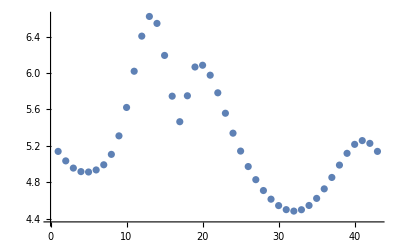

```mathematica
ListPlot[{distb, dista}//Flatten]
```

```mathematica
(*The above shows that the norm as a distance metric does not make any sense*)
```

```mathematica
(*The conclusion is that the complex roots do not intersect and therefore the simulation of the real roots proceed without any problem. But why the complex roots face linear solve error is a different question.*)
```

```mathematica
(* Now to demonstrate singularity event identification we will need to choose a different example, i.e. the moving in z direction directly hitting the singularity*)
```

## Tracking a line

Finding a new configuration to demonstrate the singularity tracking

```mathematica
newconfig = Join[{0.1, 0.2, 1.2, 0.3, -0.2, 0.1}, iksolC[{0.1, 0.2, 1.2, 0.3, -0.2, 0.1}]]//Chop
```

{0.1,0.2,1.2,0.3,-0.2,0.1,-0.133519,-0.240034,0.424393,0.71937,-0.0364687,-0.061835,0.168125,0.201993,-0.126589,-0.150554,-0.664784,-0.51192,1.56063,1.52515,1.31505,1.13009,1.12682,1.50347}

```mathematica
newconfig[[-6;;]]
```

{1.56063,1.52515,1.31505,1.13009,1.12682,1.50347}

```mathematica
rootsC = ({{x->1.6690566515409846, y->-0.5424908095031173, z->0.-0.5584446773222635 ⅈ, c1->0.-0.11895909192590448 ⅈ, c2->0.+0.7067499680438166 ⅈ, c3->0.04282342657737364}, {x->1.6690566515409846, y->-0.5424908095031173, z->0.+0.5584446773222635 ⅈ, c1->0.+0.11895909192590448 ⅈ, c2->0.-0.7067499680438166 ⅈ, c3->0.04282342657737364}, {x->-1.2782756021359538, y->1.5174785089373584, z->0.-1.003357598698621 ⅈ, c1->0.-0.6732105759400019 ⅈ, c2->0.-0.3053287106275855 ⅈ, c3->0.03992596328537696}, {x->-1.2782756021359538, y->1.5174785089373584, z->0.+1.003357598698621 ⅈ, c1->0.+0.6732105759400019 ⅈ, c2->0.+0.3053287106275855 ⅈ, c3->0.03992596328537696}, {x->-0.7265445166104874, y->-0.2158669052815546, z->-0.7100158586893778, c1->-0.15074317974801366, c2->-0.9628375006757922, c3->0.1736793034558842}, {x->0.09999999999999953, y->0.19999999999999757, z->1.200000000000001, c1->0.29999999999999827, c2->-0.19999999999999926, c3->0.10000000000000049}, {x->0.13454703785474317, y->0.2486132901326489, z->1.1707967646792576, c1->0.3568269503536564, c2->-0.2243408071634102, c3->0.10425646319074305}, {x->0.09999999999999953, y->0.19999999999999757, z->-1.200000000000001, c1->-0.29999999999999827, c2->0.19999999999999926, c3->0.10000000000000049}, {x->0.13454703785474317, y->0.2486132901326489, z->-1.1707967646792576, c1->-0.3568269503536564, c2->0.2243408071634102, c3->0.10425646319074305}, {x->-1.4673148399551303, y->-1.6778761140248597, z->0.-1.360289327654774 ⅈ, c1->0.+0.6933435678556172 ⅈ, c2->0.-0.3140857324781591 ⅈ, c3->0.037017115474116756}, {x->-1.4673148399551303, y->-1.6778761140248597, z->0.+1.360289327654774 ⅈ, c1->0.-0.6933435678556172 ⅈ, c2->0.+0.3140857324781591 ⅈ, c3->0.037017115474116756}, {x->-0.4633951982537178, y->-0.7975459604267938, z->-0.33044777665508995, c1->0.5952707609382342, c2->1.0477864396731016, c3->0.21932519683851645}, {x->-0.7265445166104874, y->-0.2158669052815546, z->0.7100158586893778, c1->0.15074317974801366, c2->0.9628375006757922, c3->0.1736793034558842}, {x->-0.4633951982537178, y->-0.7975459604267938, z->0.33044777665508995, c1->-0.5952707609382342, c2->-1.0477864396731016, c3->0.21932519683851645}})
```

{{x→1.66906,y→-0.542491,z→0.-0.558445 ⅈ,c1→0.-0.118959 ⅈ,c2→0.+0.70675 ⅈ,c3→0.0428234},{x→1.66906,y→-0.542491,z→0.+0.558445 ⅈ,c1→0.+0.118959 ⅈ,c2→0.-0.70675 ⅈ,c3→0.0428234},{x→-1.27828,y→1.51748,z→0.-1.00336 ⅈ,c1→0.-0.673211 ⅈ,c2→0.-0.305329 ⅈ,c3→0.039926},{x→-1.27828,y→1.51748,z→0.+1.00336 ⅈ,c1→0.+0.673211 ⅈ,c2→0.+0.305329 ⅈ,c3→0.039926},{x→-0.726545,y→-0.215867,z→-0.710016,c1→-0.150743,c2→-0.962838,c3→0.173679},{x→0.1,y→0.2,z→1.2,c1→0.3,c2→-0.2,c3→0.1},{x→0.134547,y→0.248613,z→1.1708,c1→0.356827,c2→-0.224341,c3→0.104256},{x→0.1,y→0.2,z→-1.2,c1→-0.3,c2→0.2,c3→0.1},{x→0.134547,y→0.248613,z→-1.1708,c1→-0.356827,c2→0.224341,c3→0.104256},{x→-1.46731,y→-1.67788,z→0.-1.36029 ⅈ,c1→0.+0.693344 ⅈ,c2→0.-0.314086 ⅈ,c3→0.0370171},{x→-1.46731,y→-1.67788,z→0.+1.36029 ⅈ,c1→0.-0.693344 ⅈ,c2→0.+0.314086 ⅈ,c3→0.0370171},{x→-0.463395,y→-0.797546,z→-0.330448,c1→0.595271,c2→1.04779,c3→0.219325},{x→-0.726545,y→-0.215867,z→0.710016,c1→0.150743,c2→0.962838,c3→0.173679},{x→-0.463395,y→-0.797546,z→0.330448,c1→-0.595271,c2→-1.04779,c3→0.219325}}

```mathematica
posesC = qx/.rootsC;
```

```mathematica
scale = 0.3;
(*parampath = {scale*Cos[α], scale*Sin[α], 1.28, scale*1, scale*0,scale*0};*)
(*parampath={scale*Cos[5*α],scale*Sin[5*α],1.5-α/10,0.3,-0.2,0.1};*)
parampath={scale,scale,1.5-α/5,0.25,-0.25,0.25};
```

```mathematica
pathpts = Table[parampath/.α->ii, {ii, 0, 2π, 2π/50}];
```

```mathematica
Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[pathpts[[u]], iksolC[pathpts[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[pathpts[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[pathpts], 1}]
```

```mathematica
legvals = Table[iksolC[pathpts[[i]]][[-6;;]], {i, Length[pathpts]}];
```

```mathematica
(*Bringing in the singluarity manifold*)
```

```mathematica
g11 = ToExpression[Import["srspm_pos_eq1.txt"]]
```

0.00218325+0.00530428 x-0.0120075 x^2-0.00132539 y-0.0292269 x y-0.0124698 y^2-0.0375001 z+0.073172 x z+0.0108431 x^2 z+0.0412325 y z+0.0468517 x y z+0.0497715 y^2 z+0.0285304 z^2-0.10733 x z^2-0.217641 y z^2+0.205157 z^3

```mathematica
lim=4;
cp=ContourPlot3D[g11==0,{x,-lim,lim},{y,-lim,lim},{z,-lim,lim},ContourStyle->Green,PlotPoints->60];
```

```mathematica
(*xpose = {0.1, 0.2, 1.2, 0.3, -0.2, 0.1};
Show[plotsrspm[Inner[Rule, qfull, Join[xpose, iksolC[xpose]], List]], cp]*)
```

```mathematica
(* Now tracking the other roots *)
```

```mathematica
posesC = Table[Join[qx/.rootsC[[i]], iksolC[qx/.rootsC[[i]]]], {i, Length[rootsC]}]//Chop;
```

```mathematica
posesC//MatrixForm
```

(1.66906 | -0.542491 | 0.-0.558445 ⅈ | 0.-0.118959 ⅈ | 0.+0.70675 ⅈ | 0.0428234 | 1.5708+1.24219 ⅈ | 1.5708+0.44073 ⅈ | 1.5708-0.557684 ⅈ | 1.5708-1.04177 ⅈ | 1.5708+0.111704 ⅈ | 1.5708+1.12026 ⅈ | 0.474064 | 0.675231 | 0.563976 | 0.864405 | 0.189338 | -0.12372 | 1.56063 | 1.52515 | 1.31505 | 1.13009 | 1.12682 | 1.50347
1.66906 | -0.542491 | 0.+0.558445 ⅈ | 0.+0.118959 ⅈ | 0.-0.70675 ⅈ | 0.0428234 | 1.5708-1.24219 ⅈ | 1.5708-0.44073 ⅈ | 1.5708+0.557684 ⅈ | 1.5708+1.04177 ⅈ | 1.5708-0.111704 ⅈ | 1.5708-1.12026 ⅈ | 0.474064 | 0.675231 | 0.563976 | 0.864405 | 0.189338 | -0.12372 | 1.56063 | 1.52515 | 1.31505 | 1.13009 | 1.12682 | 1.50347
-1.27828 | 1.51748 | 0.-1.00336 ⅈ | 0.-0.673211 ⅈ | 0.-0.305329 ⅈ | 0.039926 | -1.5708-0.821324 ⅈ | 3.14159-1.06633 ⅈ | 3.14159-0.565987 ⅈ | -1.5708-1.26154 ⅈ | -1.5708+0.759435 ⅈ | -1.5708+0.322108 ⅈ | -0.786222 | -1.5708+0.978498 ⅈ | -1.5708+1.31069 ⅈ | -1.29618 | -0.830805 | -0.870113 | 1.56063 | 1.52515 | 1.31505 | 1.13009 | 1.12682 | 1.50347
-1.27828 | 1.51748 | 0.+1.00336 ⅈ | 0.+0.673211 ⅈ | 0.+0.305329 ⅈ | 0.039926 | -1.5708+0.821324 ⅈ | 0.+1.06633 ⅈ | 0.+0.565987 ⅈ | -1.5708+1.26154 ⅈ | -1.5708-0.759435 ⅈ | -1.5708-0.322108 ⅈ | -0.786222 | -1.5708+0.978498 ⅈ | -1.5708+1.31069 ⅈ | -1.29618 | -0.830805 | -0.870113 | 1.56063 | 1.52515 | 1.31505 | 1.13009 | 1.12682 | 1.50347
-0.726545 | -0.215867 | -0.710016 | -0.150743 | -0.962838 | 0.173679 | -1.75719 | -2.3557 | 2.98104 | 2.92737 | -2.13982 | -1.66206 | 0.336236 | 0.455665 | 0.247601 | 0.366849 | -0.169063 | -0.289286 | 1.56063 | 1.52515 | 1.31505 | 1.13009 | 1.12682 | 1.50347
0.1 | 0.2 | 1.2 | 0.3 | -0.2 | 0.1 | -0.133519 | -0.240034 | 0.424393 | 0.71937 | -0.0364687 | -0.061835 | 0.168125 | 0.201993 | -0.126589 | -0.150554 | -0.664784 | -0.51192 | 1.56063 | 1.52515 | 1.31505 | 1.13009 | 1.12682 | 1.50347
0.134547 | 0.248613 | 1.1708 | 0.356827 | -0.224341 | 0.104256 | -0.120247 | -0.226552 | 0.452974 | 0.797293 | 0.0249633 | -0.0375029 | 0.155002 | 0.18993 | -0.158772 | -0.224778 | -0.763151 | -0.546913 | 1.56063 | 1.52515 | 1.31505 | 1.13009 | 1.12682 | 1.50347
0.1 | 0.2 | -1.2 | -0.3 | 0.2 | 0.1 | -3.00807 | -2.90156 | 2.7172 | 2.42222 | -3.10512 | -3.07976 | 0.168125 | 0.201993 | -0.126589 | -0.150554 | -0.664784 | -0.51192 | 1.56063 | 1.52515 | 1.31505 | 1.13009 | 1.12682 | 1.50347
0.134547 | 0.248613 | -1.1708 | -0.356827 | 0.224341 | 0.104256 | -3.02135 | -2.91504 | 2.68862 | 2.3443 | 3.11663 | -3.10409 | 0.155002 | 0.18993 | -0.158772 | -0.224778 | -0.763151 | -0.546913 | 1.56063 | 1.52515 | 1.31505 | 1.13009 | 1.12682 | 1.50347
-1.46731 | -1.67788 | 0.-1.36029 ⅈ | 0.+0.693344 ⅈ | 0.-0.314086 ⅈ | 0.0370171 | -1.5708+0.178461 ⅈ | -1.5708+0.292891 ⅈ | -3.14159-1.59507 ⅈ | 3.14159-0.494777 ⅈ | 3.14159-0.842004 ⅈ | -1.5708-0.980373 ⅈ | 0.686147 | 0.602532 | 1.5708-0.279237 ⅈ | 1.5708-1.66674 ⅈ | 1.5708-1.51139 ⅈ | 0.792573 | 1.56063 | 1.52515 | 1.31505 | 1.13009 | 1.12682 | 1.50347
-1.46731 | -1.67788 | 0.+1.36029 ⅈ | 0.-0.693344 ⅈ | 0.+0.314086 ⅈ | 0.0370171 | -1.5708-0.178461 ⅈ | -1.5708-0.292891 ⅈ | 0.+1.59507 ⅈ | 0.+0.494777 ⅈ | 0.+0.842004 ⅈ | -1.5708+0.980373 ⅈ | 0.686147 | 0.602532 | 1.5708-0.279237 ⅈ | 1.5708-1.66674 ⅈ | 1.5708-1.51139 ⅈ | 0.792573 | 1.56063 | 1.52515 | 1.31505 | 1.13009 | 1.12682 | 1.50347
-0.463395 | -0.797546 | -0.330448 | 0.595271 | 1.04779 | 0.219325 | -2.06273 | -1.36493 | 1.17061 | 2.16108 | -2.20988 | -2.18918 | 0.668026 | 1.2243 | 1.08193 | 1.20091 | 0.237323 | -0.0635839 | 1.56063 | 1.52515 | 1.31505 | 1.13009 | 1.12682 | 1.50347
-0.726545 | -0.215867 | 0.710016 | 0.150743 | 0.962838 | 0.173679 | -1.3844 | -0.785892 | 0.160551 | 0.21422 | -1.00177 | -1.47953 | 0.336236 | 0.455665 | 0.247601 | 0.366849 | -0.169063 | -0.289286 | 1.56063 | 1.52515 | 1.31505 | 1.13009 | 1.12682 | 1.50347
-0.463395 | -0.797546 | 0.330448 | -0.595271 | -1.04779 | 0.219325 | -1.07886 | -1.77666 | 1.97098 | 0.980509 | -0.931715 | -0.952417 | 0.668026 | 1.2243 | 1.08193 | 1.20091 | 0.237323 | -0.0635839 | 1.56063 | 1.52515 | 1.31505 | 1.13009 | 1.12682 | 1.50347)

```mathematica
(*The IKsolver does not agree with the FK solutions!!!! IKSolver outputs wrong values*)
```

Root 14 runs till 5 
Root 13 runs till 5 
Root 12 runs till 5

Root 9 runs till 33
Root 8 runs till 51
Root 7 runs till 33
Root 6 runs till 51
Root 5 runs till 5

Root 1 runs till 4

```mathematica
iter = 2;
testext = posesC[[5]][[;;-7]]//Chop;
tic[]
tempϕ = testext;
fulllist = {Join[tempϕ, legvals[[2]]]};
For[i=2,i≤iter, i++, 
tempϕ = NRTracking[legvals[[i]], tempϕ,cηext,cJηext];
AppendTo[fulllist, Join[tempϕ, legvals[[i]]]//Chop];
]
toc[]

fulllist[[-1]]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.69739×10^-6+0. ⅈ,2.21058×10^-6+0. ⅈ,9.51346×10^-7+0. ⅈ,-1.77523+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.000371706+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},«16»,{0.+0. ⅈ,0.+0. ⅈ,-1.+0. ⅈ,0.0000290363+0. ⅈ,«11»,0.+0. ⅈ,0.+0. ⅈ,-1.4935+0. ⅈ}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.19516×10^-11+0. ⅈ,7.14443×10^-12+0. ⅈ,3.077×10^-12+0. ⅈ,-0.0604882+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.718263+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},«16»,{0.+0. ⅈ,0.+0. ⅈ,-1.+0. ⅈ,«12»,0.+0. ⅈ,0.+0. ⅈ,0.0483022+0. ⅈ}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.32067×10^-21+0. ⅈ,7.89467×10^-22+0. ⅈ,3.40011×10^-22+0. ⅈ,-0.906881+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.340079+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{«1»},{«1»},«12»,{«1»},{«1»},{0.+0. ⅈ,0.+0. ⅈ,-1.+0. ⅈ,«12»,0.+0. ⅈ,0.+0. ⅈ,-0.671125+0. ⅈ}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

CompiledFunction::cfne: Numerical error encountered; proceeding with uncompiled evaluation.

General::munfl: 1/((3.29754×10^207+0. ⅈ)^2) is too small to represent as a normalized machine number; precision may be lost.

CompiledFunction::cfne: Numerical error encountered; proceeding with uncompiled evaluation.

General::munfl: 1/((4.21122×10^209+0. ⅈ)^2) is too small to represent as a normalized machine number; precision may be lost.

CompiledFunction::cfne: Numerical error encountered; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfne will be suppressed during this calculation.

General::munfl: 1/((1.76018×10^210+0. ⅈ)^2) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

LinearSolve::nosol: Linear equation encountered that has no solution.

General::stop: Further output of LinearSolve::nosol will be suppressed during this calculation.

CompiledFunction::cfsa: Argument (-2.35081+0. ⅈ)-LinearSolve[{{-1,0,0,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.612726+0. ⅈ,0,0,0,0,0,-0.699385+0. ⅈ,0,0,0,0,0},«16»,{0,0,-1,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0,0,0,0,0,1.61516+0. ⅈ,0,0,0,0,0,-0.217661+0. ⅈ}},{1.52958+0. ⅈ,0.576765+0. ⅈ,«14»,-1.12833+0. ⅈ,-5.38416+0. ⅈ}] at position 1 should be a machine-size complex number.

Actual time consumed: 0.17037 seconds.

CPU time consumed: 0.171095 seconds.

{-2.35081-LinearSolve[{{-1,0,0,0,0,0,0.612726,0,0,0,0,0,-0.699385,0,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,-1.67026,0,0,0,0,0},{0,0,-1,0,0,0,1.55382,0,0,0,0,0,0.275793,0,0,0,0,0},{-1,0,0,0,0,0,0,-1.31951,0,0,0,0,0,0.0457313,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,1.65755,0,0,0,0},{0,0,-1,0,0,0,0,1.00317,0,0,0,0,0,0.060152,0,0,0,0},{-1,0,0,0,0,0,0,0,-0.833946,0,0,0,0,0,-0.664179,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,1.0353,0,0,0},{0,0,-1,0,0,0,0,0,-0.613499,0,0,0,0,0,0.902837,0,0,0},{-1,0,0,0,0,0,0,0,0,1.36375,0,0,0,0,0,-0.00112396,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.36375,0,0},{0,0,-1,0,0,0,0,0,0,0.00199305,0,0,0,0,0,0.769068,0,0},{-1,0,0,0,0,0,0,0,0,0,-0.783693,0,0,0,0,0,-0.424159,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.83143,0},{0,0,-1,0,0,0,0,0,0,0,-0.27767,0,0,0,0,0,1.19714,0},{-1,0,0,0,0,0,0,0,0,0,0,1.01847,0,0,0,0,0,0.345183},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.90946},{0,0,-1,0,0,0,0,0,0,0,0,1.61516,0,0,0,0,0,-0.217661}},{1.52958,0.576765,-5.7899,1.57084,0.194616,-7.72214,2.00853,0.559193,-7.23657,1.39304,-0.380736,-5.03888,2.85169,-0.560427,-7.18632,1.46823,-1.12833,-5.38416}],0.855718-LinearSolve[{{-1,0,0,0,0,0,0.612726,0,0,0,0,0,-0.699385,0,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,-1.67026,0,0,0,0,0},{0,0,-1,0,0,0,1.55382,0,0,0,0,0,0.275793,0,0,0,0,0},{-1,0,0,0,0,0,0,-1.31951,0,0,0,0,0,0.0457313,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,1.65755,0,0,0,0},{0,0,-1,0,0,0,0,1.00317,0,0,0,0,0,0.060152,0,0,0,0},{-1,0,0,0,0,0,0,0,-0.833946,0,0,0,0,0,-0.664179,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,1.0353,0,0,0},{0,0,-1,0,0,0,0,0,-0.613499,0,0,0,0,0,0.902837,0,0,0},{-1,0,0,0,0,0,0,0,0,1.36375,0,0,0,0,0,-0.00112396,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.36375,0,0},{0,0,-1,0,0,0,0,0,0,0.00199305,0,0,0,0,0,0.769068,0,0},{-1,0,0,0,0,0,0,0,0,0,-0.783693,0,0,0,0,0,-0.424159,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.83143,0},{0,0,-1,0,0,0,0,0,0,0,-0.27767,0,0,0,0,0,1.19714,0},{-1,0,0,0,0,0,0,0,0,0,0,1.01847,0,0,0,0,0,0.345183},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.90946},{0,0,-1,0,0,0,0,0,0,0,0,1.61516,0,0,0,0,0,-0.217661}},{1.52958,0.576765,-5.7899,1.57084,0.194616,-7.72214,2.00853,0.559193,-7.23657,1.39304,-0.380736,-5.03888,2.85169,-0.560427,-7.18632,1.46823,-1.12833,-5.38416}],6.40263-LinearSolve[{{-1,0,0,0,0,0,0.612726,0,0,0,0,0,-0.699385,0,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,-1.67026,0,0,0,0,0},{0,0,-1,0,0,0,1.55382,0,0,0,0,0,0.275793,0,0,0,0,0},{-1,0,0,0,0,0,0,-1.31951,0,0,0,0,0,0.0457313,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,1.65755,0,0,0,0},{0,0,-1,0,0,0,0,1.00317,0,0,0,0,0,0.060152,0,0,0,0},{-1,0,0,0,0,0,0,0,-0.833946,0,0,0,0,0,-0.664179,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,1.0353,0,0,0},{0,0,-1,0,0,0,0,0,-0.613499,0,0,0,0,0,0.902837,0,0,0},{-1,0,0,0,0,0,0,0,0,1.36375,0,0,0,0,0,-0.00112396,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.36375,0,0},{0,0,-1,0,0,0,0,0,0,0.00199305,0,0,0,0,0,0.769068,0,0},{-1,0,0,0,0,0,0,0,0,0,-0.783693,0,0,0,0,0,-0.424159,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.83143,0},{0,0,-1,0,0,0,0,0,0,0,-0.27767,0,0,0,0,0,1.19714,0},{-1,0,0,0,0,0,0,0,0,0,0,1.01847,0,0,0,0,0,0.345183},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.90946},{0,0,-1,0,0,0,0,0,0,0,0,1.61516,0,0,0,0,0,-0.217661}},{1.52958,0.576765,-5.7899,1.57084,0.194616,-7.72214,2.00853,0.559193,-7.23657,1.39304,-0.380736,-5.03888,2.85169,-0.560427,-7.18632,1.46823,-1.12833,-5.38416}],9.36123×10^161-LinearSolve[{{-1,0,0,0,0,0,0.612726,0,0,0,0,0,-0.699385,0,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,-1.67026,0,0,0,0,0},{0,0,-1,0,0,0,1.55382,0,0,0,0,0,0.275793,0,0,0,0,0},{-1,0,0,0,0,0,0,-1.31951,0,0,0,0,0,0.0457313,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,1.65755,0,0,0,0},{0,0,-1,0,0,0,0,1.00317,0,0,0,0,0,0.060152,0,0,0,0},{-1,0,0,0,0,0,0,0,-0.833946,0,0,0,0,0,-0.664179,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,1.0353,0,0,0},{0,0,-1,0,0,0,0,0,-0.613499,0,0,0,0,0,0.902837,0,0,0},{-1,0,0,0,0,0,0,0,0,1.36375,0,0,0,0,0,-0.00112396,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.36375,0,0},{0,0,-1,0,0,0,0,0,0,0.00199305,0,0,0,0,0,0.769068,0,0},{-1,0,0,0,0,0,0,0,0,0,-0.783693,0,0,0,0,0,-0.424159,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.83143,0},{0,0,-1,0,0,0,0,0,0,0,-0.27767,0,0,0,0,0,1.19714,0},{-1,0,0,0,0,0,0,0,0,0,0,1.01847,0,0,0,0,0,0.345183},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.90946},{0,0,-1,0,0,0,0,0,0,0,0,1.61516,0,0,0,0,0,-0.217661}},{1.52958,0.576765,-5.7899,1.57084,0.194616,-7.72214,2.00853,0.559193,-7.23657,1.39304,-0.380736,-5.03888,2.85169,-0.560427,-7.18632,1.46823,-1.12833,-5.38416}],-5.31699×10^161-LinearSolve[{{-1,0,0,0,0,0,0.612726,0,0,0,0,0,-0.699385,0,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,-1.67026,0,0,0,0,0},{0,0,-1,0,0,0,1.55382,0,0,0,0,0,0.275793,0,0,0,0,0},{-1,0,0,0,0,0,0,-1.31951,0,0,0,0,0,0.0457313,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,1.65755,0,0,0,0},{0,0,-1,0,0,0,0,1.00317,0,0,0,0,0,0.060152,0,0,0,0},{-1,0,0,0,0,0,0,0,-0.833946,0,0,0,0,0,-0.664179,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,1.0353,0,0,0},{0,0,-1,0,0,0,0,0,-0.613499,0,0,0,0,0,0.902837,0,0,0},{-1,0,0,0,0,0,0,0,0,1.36375,0,0,0,0,0,-0.00112396,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.36375,0,0},{0,0,-1,0,0,0,0,0,0,0.00199305,0,0,0,0,0,0.769068,0,0},{-1,0,0,0,0,0,0,0,0,0,-0.783693,0,0,0,0,0,-0.424159,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.83143,0},{0,0,-1,0,0,0,0,0,0,0,-0.27767,0,0,0,0,0,1.19714,0},{-1,0,0,0,0,0,0,0,0,0,0,1.01847,0,0,0,0,0,0.345183},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.90946},{0,0,-1,0,0,0,0,0,0,0,0,1.61516,0,0,0,0,0,-0.217661}},{1.52958,0.576765,-5.7899,1.57084,0.194616,-7.72214,2.00853,0.559193,-7.23657,1.39304,-0.380736,-5.03888,2.85169,-0.560427,-7.18632,1.46823,-1.12833,-5.38416}],2.11377×10^162-LinearSolve[{{-1,0,0,0,0,0,0.612726,0,0,0,0,0,-0.699385,0,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,-1.67026,0,0,0,0,0},{0,0,-1,0,0,0,1.55382,0,0,0,0,0,0.275793,0,0,0,0,0},{-1,0,0,0,0,0,0,-1.31951,0,0,0,0,0,0.0457313,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,1.65755,0,0,0,0},{0,0,-1,0,0,0,0,1.00317,0,0,0,0,0,0.060152,0,0,0,0},{-1,0,0,0,0,0,0,0,-0.833946,0,0,0,0,0,-0.664179,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,1.0353,0,0,0},{0,0,-1,0,0,0,0,0,-0.613499,0,0,0,0,0,0.902837,0,0,0},{-1,0,0,0,0,0,0,0,0,1.36375,0,0,0,0,0,-0.00112396,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.36375,0,0},{0,0,-1,0,0,0,0,0,0,0.00199305,0,0,0,0,0,0.769068,0,0},{-1,0,0,0,0,0,0,0,0,0,-0.783693,0,0,0,0,0,-0.424159,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.83143,0},{0,0,-1,0,0,0,0,0,0,0,-0.27767,0,0,0,0,0,1.19714,0},{-1,0,0,0,0,0,0,0,0,0,0,1.01847,0,0,0,0,0,0.345183},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.90946},{0,0,-1,0,0,0,0,0,0,0,0,1.61516,0,0,0,0,0,-0.217661}},{1.52958,0.576765,-5.7899,1.57084,0.194616,-7.72214,2.00853,0.559193,-7.23657,1.39304,-0.380736,-5.03888,2.85169,-0.560427,-7.18632,1.46823,-1.12833,-5.38416}],-13151.9-LinearSolve[{{-1,0,0,0,0,0,0.612726,0,0,0,0,0,-0.699385,0,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,-1.67026,0,0,0,0,0},{0,0,-1,0,0,0,1.55382,0,0,0,0,0,0.275793,0,0,0,0,0},{-1,0,0,0,0,0,0,-1.31951,0,0,0,0,0,0.0457313,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,1.65755,0,0,0,0},{0,0,-1,0,0,0,0,1.00317,0,0,0,0,0,0.060152,0,0,0,0},{-1,0,0,0,0,0,0,0,-0.833946,0,0,0,0,0,-0.664179,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,1.0353,0,0,0},{0,0,-1,0,0,0,0,0,-0.613499,0,0,0,0,0,0.902837,0,0,0},{-1,0,0,0,0,0,0,0,0,1.36375,0,0,0,0,0,-0.00112396,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.36375,0,0},{0,0,-1,0,0,0,0,0,0,0.00199305,0,0,0,0,0,0.769068,0,0},{-1,0,0,0,0,0,0,0,0,0,-0.783693,0,0,0,0,0,-0.424159,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.83143,0},{0,0,-1,0,0,0,0,0,0,0,-0.27767,0,0,0,0,0,1.19714,0},{-1,0,0,0,0,0,0,0,0,0,0,1.01847,0,0,0,0,0,0.345183},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.90946},{0,0,-1,0,0,0,0,0,0,0,0,1.61516,0,0,0,0,0,-0.217661}},{1.52958,0.576765,-5.7899,1.57084,0.194616,-7.72214,2.00853,0.559193,-7.23657,1.39304,-0.380736,-5.03888,2.85169,-0.560427,-7.18632,1.46823,-1.12833,-5.38416}],3670.03-LinearSolve[{{-1,0,0,0,0,0,0.612726,0,0,0,0,0,-0.699385,0,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,-1.67026,0,0,0,0,0},{0,0,-1,0,0,0,1.55382,0,0,0,0,0,0.275793,0,0,0,0,0},{-1,0,0,0,0,0,0,-1.31951,0,0,0,0,0,0.0457313,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,1.65755,0,0,0,0},{0,0,-1,0,0,0,0,1.00317,0,0,0,0,0,0.060152,0,0,0,0},{-1,0,0,0,0,0,0,0,-0.833946,0,0,0,0,0,-0.664179,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,1.0353,0,0,0},{0,0,-1,0,0,0,0,0,-0.613499,0,0,0,0,0,0.902837,0,0,0},{-1,0,0,0,0,0,0,0,0,1.36375,0,0,0,0,0,-0.00112396,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.36375,0,0},{0,0,-1,0,0,0,0,0,0,0.00199305,0,0,0,0,0,0.769068,0,0},{-1,0,0,0,0,0,0,0,0,0,-0.783693,0,0,0,0,0,-0.424159,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.83143,0},{0,0,-1,0,0,0,0,0,0,0,-0.27767,0,0,0,0,0,1.19714,0},{-1,0,0,0,0,0,0,0,0,0,0,1.01847,0,0,0,0,0,0.345183},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.90946},{0,0,-1,0,0,0,0,0,0,0,0,1.61516,0,0,0,0,0,-0.217661}},{1.52958,0.576765,-5.7899,1.57084,0.194616,-7.72214,2.00853,0.559193,-7.23657,1.39304,-0.380736,-5.03888,2.85169,-0.560427,-7.18632,1.46823,-1.12833,-5.38416}],-2212.32-LinearSolve[{{-1,0,0,0,0,0,0.612726,0,0,0,0,0,-0.699385,0,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,-1.67026,0,0,0,0,0},{0,0,-1,0,0,0,1.55382,0,0,0,0,0,0.275793,0,0,0,0,0},{-1,0,0,0,0,0,0,-1.31951,0,0,0,0,0,0.0457313,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,1.65755,0,0,0,0},{0,0,-1,0,0,0,0,1.00317,0,0,0,0,0,0.060152,0,0,0,0},{-1,0,0,0,0,0,0,0,-0.833946,0,0,0,0,0,-0.664179,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,1.0353,0,0,0},{0,0,-1,0,0,0,0,0,-0.613499,0,0,0,0,0,0.902837,0,0,0},{-1,0,0,0,0,0,0,0,0,1.36375,0,0,0,0,0,-0.00112396,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.36375,0,0},{0,0,-1,0,0,0,0,0,0,0.00199305,0,0,0,0,0,0.769068,0,0},{-1,0,0,0,0,0,0,0,0,0,-0.783693,0,0,0,0,0,-0.424159,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.83143,0},{0,0,-1,0,0,0,0,0,0,0,-0.27767,0,0,0,0,0,1.19714,0},{-1,0,0,0,0,0,0,0,0,0,0,1.01847,0,0,0,0,0,0.345183},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.90946},{0,0,-1,0,0,0,0,0,0,0,0,1.61516,0,0,0,0,0,-0.217661}},{1.52958,0.576765,-5.7899,1.57084,0.194616,-7.72214,2.00853,0.559193,-7.23657,1.39304,-0.380736,-5.03888,2.85169,-0.560427,-7.18632,1.46823,-1.12833,-5.38416}],-1244.07-LinearSolve[{{-1,0,0,0,0,0,0.612726,0,0,0,0,0,-0.699385,0,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,-1.67026,0,0,0,0,0},{0,0,-1,0,0,0,1.55382,0,0,0,0,0,0.275793,0,0,0,0,0},{-1,0,0,0,0,0,0,-1.31951,0,0,0,0,0,0.0457313,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,1.65755,0,0,0,0},{0,0,-1,0,0,0,0,1.00317,0,0,0,0,0,0.060152,0,0,0,0},{-1,0,0,0,0,0,0,0,-0.833946,0,0,0,0,0,-0.664179,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,1.0353,0,0,0},{0,0,-1,0,0,0,0,0,-0.613499,0,0,0,0,0,0.902837,0,0,0},{-1,0,0,0,0,0,0,0,0,1.36375,0,0,0,0,0,-0.00112396,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.36375,0,0},{0,0,-1,0,0,0,0,0,0,0.00199305,0,0,0,0,0,0.769068,0,0},{-1,0,0,0,0,0,0,0,0,0,-0.783693,0,0,0,0,0,-0.424159,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.83143,0},{0,0,-1,0,0,0,0,0,0,0,-0.27767,0,0,0,0,0,1.19714,0},{-1,0,0,0,0,0,0,0,0,0,0,1.01847,0,0,0,0,0,0.345183},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.90946},{0,0,-1,0,0,0,0,0,0,0,0,1.61516,0,0,0,0,0,-0.217661}},{1.52958,0.576765,-5.7899,1.57084,0.194616,-7.72214,2.00853,0.559193,-7.23657,1.39304,-0.380736,-5.03888,2.85169,-0.560427,-7.18632,1.46823,-1.12833,-5.38416}],-1087.33-LinearSolve[{{-1,0,0,0,0,0,0.612726,0,0,0,0,0,-0.699385,0,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,-1.67026,0,0,0,0,0},{0,0,-1,0,0,0,1.55382,0,0,0,0,0,0.275793,0,0,0,0,0},{-1,0,0,0,0,0,0,-1.31951,0,0,0,0,0,0.0457313,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,1.65755,0,0,0,0},{0,0,-1,0,0,0,0,1.00317,0,0,0,0,0,0.060152,0,0,0,0},{-1,0,0,0,0,0,0,0,-0.833946,0,0,0,0,0,-0.664179,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,1.0353,0,0,0},{0,0,-1,0,0,0,0,0,-0.613499,0,0,0,0,0,0.902837,0,0,0},{-1,0,0,0,0,0,0,0,0,1.36375,0,0,0,0,0,-0.00112396,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.36375,0,0},{0,0,-1,0,0,0,0,0,0,0.00199305,0,0,0,0,0,0.769068,0,0},{-1,0,0,0,0,0,0,0,0,0,-0.783693,0,0,0,0,0,-0.424159,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.83143,0},{0,0,-1,0,0,0,0,0,0,0,-0.27767,0,0,0,0,0,1.19714,0},{-1,0,0,0,0,0,0,0,0,0,0,1.01847,0,0,0,0,0,0.345183},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.90946},{0,0,-1,0,0,0,0,0,0,0,0,1.61516,0,0,0,0,0,-0.217661}},{1.52958,0.576765,-5.7899,1.57084,0.194616,-7.72214,2.00853,0.559193,-7.23657,1.39304,-0.380736,-5.03888,2.85169,-0.560427,-7.18632,1.46823,-1.12833,-5.38416}],3319.66-LinearSolve[{{-1,0,0,0,0,0,0.612726,0,0,0,0,0,-0.699385,0,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,-1.67026,0,0,0,0,0},{0,0,-1,0,0,0,1.55382,0,0,0,0,0,0.275793,0,0,0,0,0},{-1,0,0,0,0,0,0,-1.31951,0,0,0,0,0,0.0457313,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,1.65755,0,0,0,0},{0,0,-1,0,0,0,0,1.00317,0,0,0,0,0,0.060152,0,0,0,0},{-1,0,0,0,0,0,0,0,-0.833946,0,0,0,0,0,-0.664179,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,1.0353,0,0,0},{0,0,-1,0,0,0,0,0,-0.613499,0,0,0,0,0,0.902837,0,0,0},{-1,0,0,0,0,0,0,0,0,1.36375,0,0,0,0,0,-0.00112396,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.36375,0,0},{0,0,-1,0,0,0,0,0,0,0.00199305,0,0,0,0,0,0.769068,0,0},{-1,0,0,0,0,0,0,0,0,0,-0.783693,0,0,0,0,0,-0.424159,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.83143,0},{0,0,-1,0,0,0,0,0,0,0,-0.27767,0,0,0,0,0,1.19714,0},{-1,0,0,0,0,0,0,0,0,0,0,1.01847,0,0,0,0,0,0.345183},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.90946},{0,0,-1,0,0,0,0,0,0,0,0,1.61516,0,0,0,0,0,-0.217661}},{1.52958,0.576765,-5.7899,1.57084,0.194616,-7.72214,2.00853,0.559193,-7.23657,1.39304,-0.380736,-5.03888,2.85169,-0.560427,-7.18632,1.46823,-1.12833,-5.38416}],-6.70613-LinearSolve[{{-1,0,0,0,0,0,0.612726,0,0,0,0,0,-0.699385,0,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,-1.67026,0,0,0,0,0},{0,0,-1,0,0,0,1.55382,0,0,0,0,0,0.275793,0,0,0,0,0},{-1,0,0,0,0,0,0,-1.31951,0,0,0,0,0,0.0457313,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,1.65755,0,0,0,0},{0,0,-1,0,0,0,0,1.00317,0,0,0,0,0,0.060152,0,0,0,0},{-1,0,0,0,0,0,0,0,-0.833946,0,0,0,0,0,-0.664179,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,1.0353,0,0,0},{0,0,-1,0,0,0,0,0,-0.613499,0,0,0,0,0,0.902837,0,0,0},{-1,0,0,0,0,0,0,0,0,1.36375,0,0,0,0,0,-0.00112396,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.36375,0,0},{0,0,-1,0,0,0,0,0,0,0.00199305,0,0,0,0,0,0.769068,0,0},{-1,0,0,0,0,0,0,0,0,0,-0.783693,0,0,0,0,0,-0.424159,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.83143,0},{0,0,-1,0,0,0,0,0,0,0,-0.27767,0,0,0,0,0,1.19714,0},{-1,0,0,0,0,0,0,0,0,0,0,1.01847,0,0,0,0,0,0.345183},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.90946},{0,0,-1,0,0,0,0,0,0,0,0,1.61516,0,0,0,0,0,-0.217661}},{1.52958,0.576765,-5.7899,1.57084,0.194616,-7.72214,2.00853,0.559193,-7.23657,1.39304,-0.380736,-5.03888,2.85169,-0.560427,-7.18632,1.46823,-1.12833,-5.38416}],386.461-LinearSolve[{{-1,0,0,0,0,0,0.612726,0,0,0,0,0,-0.699385,0,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,-1.67026,0,0,0,0,0},{0,0,-1,0,0,0,1.55382,0,0,0,0,0,0.275793,0,0,0,0,0},{-1,0,0,0,0,0,0,-1.31951,0,0,0,0,0,0.0457313,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,1.65755,0,0,0,0},{0,0,-1,0,0,0,0,1.00317,0,0,0,0,0,0.060152,0,0,0,0},{-1,0,0,0,0,0,0,0,-0.833946,0,0,0,0,0,-0.664179,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,1.0353,0,0,0},{0,0,-1,0,0,0,0,0,-0.613499,0,0,0,0,0,0.902837,0,0,0},{-1,0,0,0,0,0,0,0,0,1.36375,0,0,0,0,0,-0.00112396,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.36375,0,0},{0,0,-1,0,0,0,0,0,0,0.00199305,0,0,0,0,0,0.769068,0,0},{-1,0,0,0,0,0,0,0,0,0,-0.783693,0,0,0,0,0,-0.424159,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.83143,0},{0,0,-1,0,0,0,0,0,0,0,-0.27767,0,0,0,0,0,1.19714,0},{-1,0,0,0,0,0,0,0,0,0,0,1.01847,0,0,0,0,0,0.345183},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.90946},{0,0,-1,0,0,0,0,0,0,0,0,1.61516,0,0,0,0,0,-0.217661}},{1.52958,0.576765,-5.7899,1.57084,0.194616,-7.72214,2.00853,0.559193,-7.23657,1.39304,-0.380736,-5.03888,2.85169,-0.560427,-7.18632,1.46823,-1.12833,-5.38416}],-995.06-LinearSolve[{{-1,0,0,0,0,0,0.612726,0,0,0,0,0,-0.699385,0,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,-1.67026,0,0,0,0,0},{0,0,-1,0,0,0,1.55382,0,0,0,0,0,0.275793,0,0,0,0,0},{-1,0,0,0,0,0,0,-1.31951,0,0,0,0,0,0.0457313,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,1.65755,0,0,0,0},{0,0,-1,0,0,0,0,1.00317,0,0,0,0,0,0.060152,0,0,0,0},{-1,0,0,0,0,0,0,0,-0.833946,0,0,0,0,0,-0.664179,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,1.0353,0,0,0},{0,0,-1,0,0,0,0,0,-0.613499,0,0,0,0,0,0.902837,0,0,0},{-1,0,0,0,0,0,0,0,0,1.36375,0,0,0,0,0,-0.00112396,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.36375,0,0},{0,0,-1,0,0,0,0,0,0,0.00199305,0,0,0,0,0,0.769068,0,0},{-1,0,0,0,0,0,0,0,0,0,-0.783693,0,0,0,0,0,-0.424159,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.83143,0},{0,0,-1,0,0,0,0,0,0,0,-0.27767,0,0,0,0,0,1.19714,0},{-1,0,0,0,0,0,0,0,0,0,0,1.01847,0,0,0,0,0,0.345183},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.90946},{0,0,-1,0,0,0,0,0,0,0,0,1.61516,0,0,0,0,0,-0.217661}},{1.52958,0.576765,-5.7899,1.57084,0.194616,-7.72214,2.00853,0.559193,-7.23657,1.39304,-0.380736,-5.03888,2.85169,-0.560427,-7.18632,1.46823,-1.12833,-5.38416}],-691.664-LinearSolve[{{-1,0,0,0,0,0,0.612726,0,0,0,0,0,-0.699385,0,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,-1.67026,0,0,0,0,0},{0,0,-1,0,0,0,1.55382,0,0,0,0,0,0.275793,0,0,0,0,0},{-1,0,0,0,0,0,0,-1.31951,0,0,0,0,0,0.0457313,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,1.65755,0,0,0,0},{0,0,-1,0,0,0,0,1.00317,0,0,0,0,0,0.060152,0,0,0,0},{-1,0,0,0,0,0,0,0,-0.833946,0,0,0,0,0,-0.664179,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,1.0353,0,0,0},{0,0,-1,0,0,0,0,0,-0.613499,0,0,0,0,0,0.902837,0,0,0},{-1,0,0,0,0,0,0,0,0,1.36375,0,0,0,0,0,-0.00112396,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.36375,0,0},{0,0,-1,0,0,0,0,0,0,0.00199305,0,0,0,0,0,0.769068,0,0},{-1,0,0,0,0,0,0,0,0,0,-0.783693,0,0,0,0,0,-0.424159,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.83143,0},{0,0,-1,0,0,0,0,0,0,0,-0.27767,0,0,0,0,0,1.19714,0},{-1,0,0,0,0,0,0,0,0,0,0,1.01847,0,0,0,0,0,0.345183},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.90946},{0,0,-1,0,0,0,0,0,0,0,0,1.61516,0,0,0,0,0,-0.217661}},{1.52958,0.576765,-5.7899,1.57084,0.194616,-7.72214,2.00853,0.559193,-7.23657,1.39304,-0.380736,-5.03888,2.85169,-0.560427,-7.18632,1.46823,-1.12833,-5.38416}],192.628-LinearSolve[{{-1,0,0,0,0,0,0.612726,0,0,0,0,0,-0.699385,0,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,-1.67026,0,0,0,0,0},{0,0,-1,0,0,0,1.55382,0,0,0,0,0,0.275793,0,0,0,0,0},{-1,0,0,0,0,0,0,-1.31951,0,0,0,0,0,0.0457313,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,1.65755,0,0,0,0},{0,0,-1,0,0,0,0,1.00317,0,0,0,0,0,0.060152,0,0,0,0},{-1,0,0,0,0,0,0,0,-0.833946,0,0,0,0,0,-0.664179,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,1.0353,0,0,0},{0,0,-1,0,0,0,0,0,-0.613499,0,0,0,0,0,0.902837,0,0,0},{-1,0,0,0,0,0,0,0,0,1.36375,0,0,0,0,0,-0.00112396,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.36375,0,0},{0,0,-1,0,0,0,0,0,0,0.00199305,0,0,0,0,0,0.769068,0,0},{-1,0,0,0,0,0,0,0,0,0,-0.783693,0,0,0,0,0,-0.424159,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.83143,0},{0,0,-1,0,0,0,0,0,0,0,-0.27767,0,0,0,0,0,1.19714,0},{-1,0,0,0,0,0,0,0,0,0,0,1.01847,0,0,0,0,0,0.345183},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.90946},{0,0,-1,0,0,0,0,0,0,0,0,1.61516,0,0,0,0,0,-0.217661}},{1.52958,0.576765,-5.7899,1.57084,0.194616,-7.72214,2.00853,0.559193,-7.23657,1.39304,-0.380736,-5.03888,2.85169,-0.560427,-7.18632,1.46823,-1.12833,-5.38416}],-354.789-LinearSolve[{{-1,0,0,0,0,0,0.612726,0,0,0,0,0,-0.699385,0,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,-1.67026,0,0,0,0,0},{0,0,-1,0,0,0,1.55382,0,0,0,0,0,0.275793,0,0,0,0,0},{-1,0,0,0,0,0,0,-1.31951,0,0,0,0,0,0.0457313,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,1.65755,0,0,0,0},{0,0,-1,0,0,0,0,1.00317,0,0,0,0,0,0.060152,0,0,0,0},{-1,0,0,0,0,0,0,0,-0.833946,0,0,0,0,0,-0.664179,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,1.0353,0,0,0},{0,0,-1,0,0,0,0,0,-0.613499,0,0,0,0,0,0.902837,0,0,0},{-1,0,0,0,0,0,0,0,0,1.36375,0,0,0,0,0,-0.00112396,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.36375,0,0},{0,0,-1,0,0,0,0,0,0,0.00199305,0,0,0,0,0,0.769068,0,0},{-1,0,0,0,0,0,0,0,0,0,-0.783693,0,0,0,0,0,-0.424159,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.83143,0},{0,0,-1,0,0,0,0,0,0,0,-0.27767,0,0,0,0,0,1.19714,0},{-1,0,0,0,0,0,0,0,0,0,0,1.01847,0,0,0,0,0,0.345183},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.90946},{0,0,-1,0,0,0,0,0,0,0,0,1.61516,0,0,0,0,0,-0.217661}},{1.52958,0.576765,-5.7899,1.57084,0.194616,-7.72214,2.00853,0.559193,-7.23657,1.39304,-0.380736,-5.03888,2.85169,-0.560427,-7.18632,1.46823,-1.12833,-5.38416}],1.83166,1.65927,1.52581,1.56565,1.518,1.95258}

```mathematica
Manipulate[
Show[plotsrspm[Inner[Rule, qfull, fulllist[[u]], List]],Graphics3D[{Red, Sphere[Chop[fulllist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, iter, 1}]
```

Part::partw: Part 51 of {{-0.726545,-0.215867,-0.710016,-0.150743,-0.962838,0.173679,-1.75719,-2.3557,2.98104,«7»,-0.169063,-0.289286,1.83166+0. ⅈ,1.65927+0. ⅈ,1.52581+0. ⅈ,1.56565+0. ⅈ,1.518+0. ⅈ,1.95258+0. ⅈ},«23»,{«1»}} does not exist.

Inner::heads: Heads Part and List at positions 3 and 2 are expected to be the same.

ReplaceAll::reps: {Inner[Rule,{x,y,z,c1,c2,c3,ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ψ1,ψ2,ψ3,ψ4,ψ5,ψ6,l1,l2,l3,l4,l5,l6},{«1»}⟦51⟧,List]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 51 of {{-0.726545,-0.215867,-0.710016,-0.150743,-0.962838,0.173679,-1.75719,-2.3557,2.98104,2.92737,«5»,0.366849,-0.169063,-0.289286,1.83166,1.65927,1.52581,1.56565,1.518,1.95258},{«1»},«22»,{«1»}} does not exist.

Inner::heads: Heads Part and List at positions 3 and 2 are expected to be the same.

Part::take: Cannot take positions 1 through 51 in {{-0.726545,-0.215867,-0.710016,-0.150743,-0.962838,0.173679,-1.75719,-2.3557,2.98104,«7»,-0.169063,-0.289286,1.83166+0. ⅈ,1.65927+0. ⅈ,1.52581+0. ⅈ,1.56565+0. ⅈ,1.518+0. ⅈ,1.95258+0. ⅈ},«23»,{«1»}}.

Part::take: Cannot take positions 1 through 51 in {{-0.726545,-0.215867,-0.710016,-0.150743,-0.962838,0.173679,-1.75719,-2.3557,2.98104,2.92737,«5»,0.366849,-0.169063,-0.289286,1.83166,1.65927,1.52581,1.56565,1.518,1.95258},{«1»},«22»,{«1»}}.

Part::take: Cannot take positions 1 through 3 in 1;;51.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 51 of {{-0.726545,-0.215867,-0.710016,-0.150743,-0.962838,0.173679,-1.75719,-2.3557,2.98104,«7»,-0.169063,-0.289286,1.83166+0. ⅈ,1.65927+0. ⅈ,1.52581+0. ⅈ,1.56565+0. ⅈ,1.518+0. ⅈ,1.95258+0. ⅈ}} does not exist.

Inner::heads: Heads Part and List at positions 3 and 2 are expected to be the same.

ReplaceAll::reps: {Inner[Rule,{x,y,z,c1,c2,c3,ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ψ1,ψ2,ψ3,ψ4,ψ5,ψ6,l1,l2,l3,l4,l5,l6},{{-0.726545,-0.215867,-0.710016,-0.150743,-0.962838,0.173679,-1.75719,«11»,1.83166+0. ⅈ,1.65927+0. ⅈ,1.52581+0. ⅈ,1.56565+0. ⅈ,1.518+0. ⅈ,1.95258+0. ⅈ}}⟦51⟧,List]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 51 of {{-0.726545,-0.215867,-0.710016,-0.150743,-0.962838,0.173679,-1.75719,-2.3557,2.98104,2.92737,«4»,0.247601,0.366849,-0.169063,-0.289286,1.83166,1.65927,1.52581,1.56565,1.518,1.95258}} does not exist.

Inner::heads: Heads Part and List at positions 3 and 2 are expected to be the same.

Part::take: Cannot take positions 1 through 51 in {{-0.726545,-0.215867,-0.710016,-0.150743,-0.962838,0.173679,-1.75719,-2.3557,2.98104,«7»,-0.169063,-0.289286,1.83166+0. ⅈ,1.65927+0. ⅈ,1.52581+0. ⅈ,1.56565+0. ⅈ,1.518+0. ⅈ,1.95258+0. ⅈ}}.

Part::take: Cannot take positions 1 through 51 in {{-0.726545,-0.215867,-0.710016,-0.150743,-0.962838,0.173679,-1.75719,-2.3557,2.98104,2.92737,«4»,0.247601,0.366849,-0.169063,-0.289286,1.83166,1.65927,1.52581,1.56565,1.518,1.95258}}.

Part::take: Cannot take positions 1 through 3 in {{-0.726545,-0.215867,-0.710016,-0.150743,-0.962838,0.173679,-1.75719,-2.3557,2.98104,2.92737,«4»,0.247601,0.366849,-0.169063,-0.289286,1.83166,1.65927,1.52581,1.56565,1.518,1.95258}}.

General::stop: Further output of Part::take will be suppressed during this calculation.

```mathematica
Table[Det[cJηext@@fulllist[[ii]]], {ii, 1, Length[fulllist]}]//Chop
```

{64.6304}

```mathematica
14
```

{0.127588,0.0615458,0.065977,0.0656324,0.0195333}

```mathematica
13
```

{0.0680377,0.044635,0.045742,0.0391018,0.0154999}

{-41.355,-14.2528,-15.7551,-11.6206,-1.4073}

```mathematica
12
```

{0.127588,0.0615458,0.065977,0.0656324,0.0195333}

```mathematica
9
```

{0.042588,0.0770372,0.0734607,0.0934069,0.130044,0.152505,0.15749,0.167824,0.168873,0.123604,0.081405,0.0549231,0.0503217,0.0698817,0.109465,0.150995,0.16763,0.179697,0.153015,0.103421,0.0592569,0.0317075,0.0261823,0.0449864,0.0854592,0.133903,0.164686,0.166535,0.132181,0.0810302,0.0355971,0.00734366,0.000947948}

{20.7302,21.8891,17.2383,16.7752,18.0779,19.0319,19.2681,19.5189,19.733,18.2239,13.9051,9.0941,6.83094,7.13143,8.33312,9.16855,9.44307,9.56249,9.48883,8.32317,5.62747,2.94037,1.97812,2.51251,3.45769,4.0795,4.28775,4.31744,4.16621,3.37578,1.78888,0.364535,0.0382032}

```mathematica
8
```

{0.0386853,0.0618283,0.0591099,0.0714264,0.0922244,0.110895,0.121246,0.122353,0.112746,0.0918118,0.0662048,0.0472245,0.0435604,0.0574051,0.081715,0.103967,0.116385,0.117746,0.106279,0.0814213,0.0513942,0.0291953,0.0243657,0.0397821,0.0681757,0.0948971,0.109987,0.111639,0.0977118,0.0679931,0.0329025,0.007215,0.000945621,0.0178112,0.0508059,0.0831132,0.101741,0.103693,0.0864086,0.0507042,0.0100931,0.0183566,0.0255867,0.00910415,0.0285766,0.0677998,0.0912352,0.0934362,0.0714504,0.0285632,0.01696}

```mathematica
7
```

{0.042588,0.0770372,0.0734607,0.0934069,0.130044,0.152505,0.15749,0.167824,0.168873,0.123604,0.081405,0.0549231,0.0503217,0.0698817,0.109465,0.150995,0.16763,0.179697,0.153015,0.103421,0.0592569,0.0317075,0.0261823,0.0449864,0.0854592,0.133903,0.164686,0.166535,0.132181,0.0810302,0.0355971,0.00734366,0.000947948}

{-20.7302,-21.8891,-17.2383,-16.7752,-18.0779,-19.0319,-19.2681,-19.5189,-19.733,-18.2239,-13.9051,-9.0941,-6.83094,-7.13143,-8.33312,-9.16855,-9.44307,-9.56249,-9.48883,-8.32317,-5.62747,-2.94037,-1.97812,-2.51251,-3.45769,-4.0795,-4.28775,-4.31744,-4.16621,-3.37578,-1.78888,-0.364535,-0.0382032}

```mathematica
5
```

{0.0680377,0.044635,0.045742,0.0391018,0.0154999}

{41.355,14.2528,15.7551,11.6206,1.4073}

```mathematica
6
```

{0.0386853,0.0618283,0.0591099,0.0714264,0.0922244,0.110895,0.121246,0.122353,0.112746,0.0918118,0.0662048,0.0472245,0.0435604,0.0574051,0.081715,0.103967,0.116385,0.117746,0.106279,0.0814213,0.0513942,0.0291953,0.0243657,0.0397821,0.0681757,0.0948971,0.109987,0.111639,0.0977118,0.0679931,0.0329025,0.007215,0.000945621,0.0178112,0.0508059,0.0831132,0.101741,0.103693,0.0864086,0.0507042,0.0100931,0.0183566,0.0255867,0.00910415,0.0285766,0.0677998,0.0912352,0.0934362,0.0714504,0.0285632,0.01696}

```mathematica
(*Looking at the smallest singular value is not helpful as they are not monotonic as we approach sigularity, however det looks somewhat believable for most of the roots. Increasing the legval discretisation to confirm it*)
```

```mathematica
(*Increasing the legval disc still shows a parabolic change in Jetaphi, which is not wrong as singularity imples small Jeta but not vice versa. So rather than checking Jeta at each iteration, just check the convergence of the next step and if it fails we can assume that it is due to encountering a singularity. What might be other reasons for convergance to fail? Apart from starting from an extremely bad initial guess*)
```